## Attenuators in both the arms of Mach-Zehnder

## Setup

#### Beam splitter transformation

```mathematica
B[r_,t_]={{t,-r},{r,t}};
```

```mathematica
(* Creation operators are representated by c *)
```

#### First beam splitter

```mathematica
{ca0,cb0}=B[1/(√2),1/(√2)].{ca1,cb1};
```

#### Phase shift in lower path

```mathematica
cb1=ⅇ^(-ⅈ ϕ)cb2;
```

#### Second and ‘Fourth’ beam splitters

```mathematica
{ca1,cc1}=B[𝓇,𝓉].{ca2,cc2};
{cb2,cd1}=B[𝓇,𝓉].{cb3,cd2};
```

#### Third beam splitter

```mathematica
{cc2,cd2}=B[1/(√2),1/(√2)].{cc3,cd3};
```

## 1. Single-Mode Squeezed Vacuum

### SMSV in mode a

```mathematica
ClearAll[S,out]
S[ξ_,n_]=1/(√Cosh[ξ])∑_(k=0)^n √Binomial[2k,k](-Tanh[ξ]/2)^k ca0^(2k)/(√((2k)!)); (* Source: Wikipedia*)
(* S[ξ,n] approximates single mode squeezed vacuum up to photon number = 2n *)
out[ca2_,cb3_,n_]=S[ξ,n];
Prob[n_,ξ_]=Sech[ξ]∑_(k=0)^n Binomial[2k,k](Tanh[ξ]/2)^(2k);
```

### Result (BS1,3 are 50-50 beam splitters and we post select on modes a and b having vacuum)

```mathematica
cof=CoefficientList[Expand[out[ca2,cb3,2]],{ca2,cb3}];
cof2=CoefficientList[Collect[Simplify[cof[[1,1]]],{cc3,cd3}],{cc3,cd3}];
Simplify[cof2[[1,1]]]
{Simplify[cof2[[2,1]]],Simplify[cof2[[1,2]]]}
Simplify[cof2[[2,2]]]
{Simplify[cof2[[3,1]]],Simplify[cof2[[1,3]]]}
Simplify[cof2[[3,3]]]
```

1/(√Cosh[ξ])

{0,0}

(ⅇ^(-2 ⅈ ϕ) (-1+ⅇ^(2 ⅈ ϕ)) 𝓇^2 Sinh[ξ])/(4 Cosh[ξ]^(3/2))

{-(ⅇ^(-2 ⅈ ϕ) (-1+ⅇ^(ⅈ ϕ))^2 𝓇^2 Sinh[ξ])/(8 Cosh[ξ]^(3/2)),-(ⅇ^(-2 ⅈ ϕ) (1+ⅇ^(ⅈ ϕ))^2 𝓇^2 Sinh[ξ])/(8 Cosh[ξ]^(3/2))}

(3 ⅇ^(-4 ⅈ ϕ) (-1+ⅇ^(2 ⅈ ϕ))^2 𝓇^4 Sinh[ξ]^2)/(64 Cosh[ξ]^(5/2))

So the output state is

1/(√Cosh[ξ])0,0
+ ((ⅇ^(-2 ⅈ ϕ) (-1+ⅇ^(2 ⅈ ϕ)) 𝓇^2 Sinh[ξ])/(4 Cosh[ξ]^(3/2)))1,1
+ √2(-(ⅇ^(-2 ⅈ ϕ) (-1+ⅇ^(ⅈ ϕ))^2 𝓇^2 Sinh[ξ])/(8 Cosh[ξ]^(3/2)))2,0
+√2(-(ⅇ^(-2 ⅈ ϕ) (1+ⅇ^(ⅈ ϕ))^2 𝓇^2 Sinh[ξ])/(8 Cosh[ξ]^(3/2)))0,2
+2((3 ⅇ^(-4 ⅈ ϕ) (-1+ⅇ^(2 ⅈ ϕ))^2 𝓇^4 Sinh[ξ]^2)/(64 Cosh[ξ]^(5/2)))2,2
+ …

### Observing interference with and without postselection on modes a and b

#### c=1,d=1

```mathematica
ClearAll[n,a,b,c,d,wopostselect,wpostselect]
n=5;  (* Squeezed states approximated with 2n terms *)
a=0;  (* postselection on mode a *)
b=0;  (* postselection on mode b *)
c=1; (* amplitude for mode c chosen to observe the interference  *)
d=1;(* amplitude for mode d chosen to observe the interference  *)
wopostselect[ϕ_,𝓇_,ξ_] = Module[{coeffψ,coefftable},
𝓉=√(1-𝓇^2);
coeffψ =√(c!d!)CoefficientList[CoefficientList[out[ca,cb,n],{cc3,cd3}][[c+1,d+1]],{ca,cb}];
coefftable=Table[Abs[√((i-1)!   (j-1)!)coeffψ[[i,j]]]^2,{i,1,Dimensions[coeffψ][[1]]},{j,1,Dimensions[coeffψ][[2]]}];
Total[Total[coefftable]]/Prob[n,ξ]
];
wpostselect[ϕ_,𝓇_,ξ_]=Module[{},
𝓉=√(1-𝓇^2);
Abs[√(c!d! a!b!)CoefficientList[CoefficientList[out[ca,cb,n],{cc3,cd3}][[c+1,d+1]],{ca,cb}][[a+1,b+1]]]^2/Prob[n,ξ]
];
Vwo[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=FindMaximum[wopostselect [x,𝓇,ξ],{x,3 π/4}][[1]];
Imin = FindMinimum[wopostselect [x,𝓇,ξ],{x,3 π/4}][[1]];
N[(Imax-Imin)/(Imax+ Imin)]
];
Vw[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=FindMaximum[wpostselect[x,𝓇,ξ],{x,3 π/4}][[1]];
Imin = FindMinimum[wpostselect [x,𝓇,ξ],{x,3 π/4}][[1]];
N[(Imax-Imin)/(Imax+ Imin)]
];
(*Manipulate[Plot[{wopostselect [ϕ,𝓇,ξ],wpostselect[ϕ,𝓇,ξ]},{ϕ,0,2π},PlotLabel-> "Visibility (w/o , w ) postselection = ("<>ToString[Vwo[𝓇,ξ]]<>" , "<>ToString[Vw[𝓇,ξ]]<>")",AxesLabel-> {ϕ,P},PlotLegends->{"Without postselection","With postselection"},Ticks->{{0,π/2,π,(3π)/2,2π},Automatic},PlotStyle-> {Solid,Dashed},PlotRange->Full,ImageSize->Medium],{ξ,5,10,Appearance-> "Open"},{𝓇,0.1,1,Appearance-> "Open"}]*)
```

```mathematica
FindMaximum[{wopostselect[π/2,𝓇,ξ],0≤𝓇≤1&&0<ξ},{𝓇,0.5},{ξ,1}]
```

{0.0729491,{𝓇→0.609028,ξ→7.23793}}

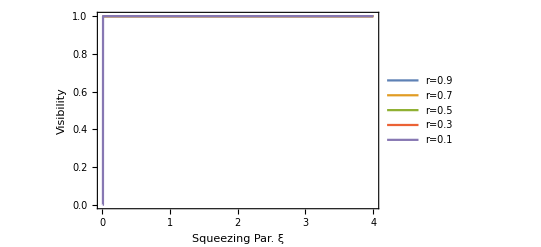

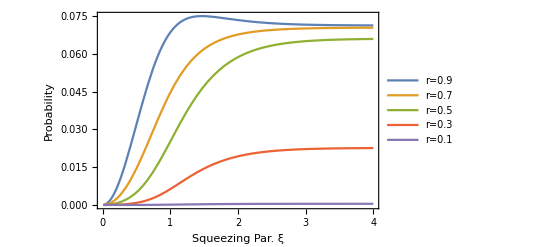

```mathematica
ClearAll[𝓇,ξ]
Plot[{Vwo[0.9,ξ],Vwo[0.7,ξ],Vwo[0.5,ξ],Vwo[0.3,ξ],Vwo[0.1,ξ]},{ξ,0.01,4},PlotRange->Full,Frame->True,FrameLabel->{"Squeezing Par. ξ","Visibility","Vis. w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,ImageSize->Scaled[0.25]]
Plot[{wopostselect[π/2,0.9,ξ],wopostselect[π/2,0.7,ξ],wopostselect[π/2,0.5,ξ],wopostselect[π/2,0.3,ξ],wopostselect[π/2,0.1,ξ]},{ξ,0.01,4},PlotRange->{0,Full},Frame->True,FrameLabel->{"Squeezing Par. ξ","Probability","Max Prob. of Success w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,ImageSize->Scaled[0.30]]
ClearAll[𝓇,ξ]
```

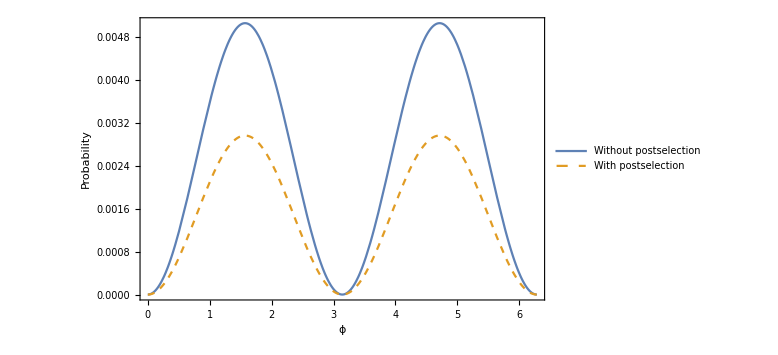

```mathematica
𝓇=0.5;
ξ=0.5;
Plot[{wopostselect[ϕ,𝓇,ξ],wpostselect[ϕ,𝓇,ξ]},{ϕ,0,2π},FrameLabel-> {"ϕ","Probability","Visibility (w/o , w ) postselection = ("<>ToString[Vwo[𝓇,ξ]]<>" , "<>ToString[Vw[𝓇,ξ]]<>") for 𝓇=0.5, ξ=1.462"},Frame-> True,PlotLegends->{"Without postselection","With postselection"},PlotStyle-> {Solid,Dashed},PlotRange->{0,Automatic},Ticks->{{0,π/2,π,(3π)/2,2π},Automatic},ImageSize->Large,LabelStyle->Large]
ClearAll[𝓇,ξ]
```

#### c=2,d=2

```mathematica
ClearAll[n,a,b,c,d,wopostselect,wpostselect]
n=10;  (* Squeezed states approximated with 2n terms *)
a=0;  (* postselection on mode a *)
b=0;  (* postselection on mode b *)
c=2; (* amplitude for mode c chosen to observe the interference  *)
d=2;(* amplitude for mode d chosen to observe the interference  *)
wopostselect[ϕ_,𝓇_,ξ_] = Module[{coeffψ,coefftable},
𝓉=√(1-𝓇^2);
coeffψ =√(c!d!)CoefficientList[CoefficientList[out[ca,cb,n],{cc3,cd3}][[c+1,d+1]],{ca,cb}];
coefftable=Table[Abs[√((i-1)!   (j-1)!)coeffψ[[i,j]]]^2,{i,1,Dimensions[coeffψ][[1]]},{j,1,Dimensions[coeffψ][[2]]}];
Total[Total[coefftable]]/Prob[n,ξ]
];
wpostselect[ϕ_,𝓇_,ξ_]=Module[{},
𝓉=√(1-𝓇^2);
Abs[√(c!d! a!b!)CoefficientList[CoefficientList[out[ca,cb,n],{cc3,cd3}][[c+1,d+1]],{ca,cb}][[a+1,b+1]]]^2/Prob[n,ξ]
];
Vwo[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=FindMaximum[wopostselect [x,𝓇,ξ],{x,3 π/4}][[1]];
Imin = FindMinimum[wopostselect [x,𝓇,ξ],{x,3 π/4}][[1]];
N[(Imax-Imin)/(Imax+ Imin)]
];
Vw[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=FindMaximum[wpostselect[x,𝓇,ξ],{x,3 π/4}][[1]];
Imin = FindMinimum[wpostselect [x,𝓇,ξ],{x,3 π/4}][[1]];
N[(Imax-Imin)/(Imax+ Imin)]
];
(*Manipulate[Plot[{wopostselect [ϕ,𝓇,ξ],wpostselect[ϕ,𝓇,ξ]},{ϕ,0,2π},PlotLabel-> "Visibility (w/o , w ) postselection = ("<>ToString[Vwo[𝓇,ξ]]<>" , "<>ToString[Vw[𝓇,ξ]]<>")",AxesLabel-> {ϕ,P},PlotLegends->{"Without postselection","With postselection"},Ticks->{{0,π/2,π,(3π)/2,2π},Automatic},PlotStyle-> {Solid,Dashed},PlotRange->Full,ImageSize->Medium],{ξ,5,10,Appearance-> "Open"},{𝓇,0.1,1,Appearance-> "Open"}]*)
```

{0.0419302,{𝓇→1.,ξ→1.61082}}

FindMaximum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a maximum; it may be a minimum or a saddle point.

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

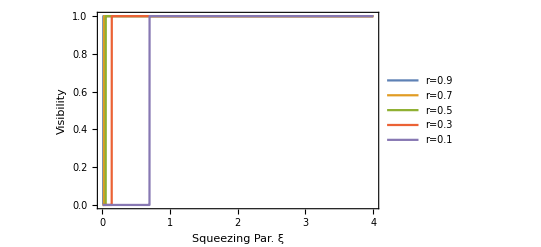

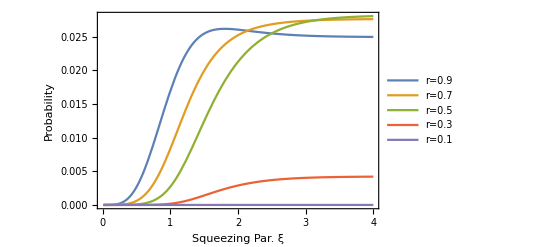

```mathematica
ClearAll[𝓇,ξ]
FindMaximum[{wopostselect[π/2,𝓇,ξ],0≤𝓇≤1&&0<ξ},{𝓇,0.5},{ξ,1}]
Plot[{Vwo[0.9,ξ],Vwo[0.7,ξ],Vwo[0.5,ξ],Vwo[0.3,ξ],Vwo[0.1,ξ]},{ξ,0.01,4},PlotRange->Full,Frame->True,FrameLabel->{"Squeezing Par. ξ","Visibility","Vis. w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,ImageSize->Scaled[0.25]]
Plot[{wopostselect[π/2,0.9,ξ],wopostselect[π/2,0.7,ξ],wopostselect[π/2,0.5,ξ],wopostselect[π/2,0.3,ξ],wopostselect[π/2,0.1,ξ]},{ξ,0.01,4},PlotRange->{0,Full},Frame->True,FrameLabel->{"Squeezing Par. ξ","Probability","Max Prob. of Success w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,ImageSize->Scaled[0.30]]
ClearAll[𝓇,ξ]
```

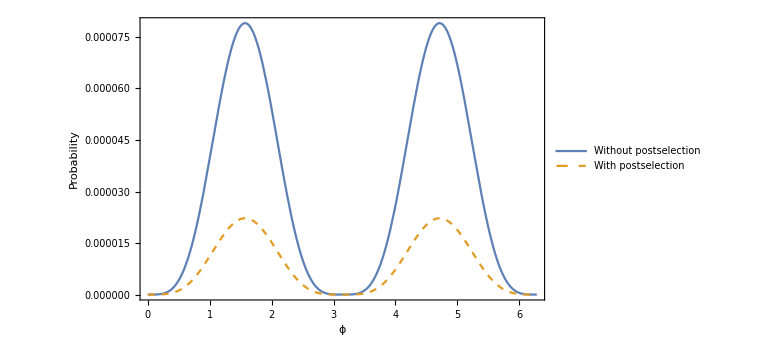

```mathematica
ClearAll[𝓇,ξ]
𝓇=0.5;
ξ=0.5;
Plot[{wopostselect[ϕ,𝓇,ξ],wpostselect[ϕ,𝓇,ξ]},{ϕ,0,2π},FrameLabel-> {"ϕ","Probability","Visibility (w/o , w ) postselection = ("<>ToString[Vwo[𝓇,ξ]]<>" , "<>ToString[Vw[𝓇,ξ]]<>") for 𝓇=0.5, ξ=1.462"},Frame-> True,PlotLegends->{"Without postselection","With postselection"},PlotStyle-> {Solid,Dashed},PlotRange->{0,Automatic},Ticks->{{0,π/2,π,(3π)/2,2π},Automatic},ImageSize->Large,LabelStyle->Large]
ClearAll[𝓇,ξ]
```

## 2. Two-Mode Squeezed Vacuum Input and observing interference for P(1,1)

```mathematica
(* T[ξ_,n_]=1/Cosh[ξ]∑_(k=0)^n (-Tanh[ξ]/1)^k(ca0^k cb0^k)/(k!); (* Source: Wikipedia*)*)
(* T[ξ,n] approximates two mode squeezed vacuum up to photon number = n,n *)
ClearAll[out2,n]
n=5;
out2[ca2_,cb3_]=1/Cosh[ξ] Sum[(-Tanh[ξ]/1 ca0 cb0)^k/k!,{k,0,n}];
Prob[n_,ξ_]=Sech[ξ]^2(1-Tanh[ξ]^(2(n+1)))/(1-Tanh[ξ]^2);
```

```mathematica
(* Approximation of taking only a few terms *)
```

```mathematica
ClearAll[a,b,c,d,wopostselect2,wpostselect2]
a=0;  (* postselection on mode a *)
b=0;  (* postselection on mode b *)
c=1; (* amplitude for mode c chosen to observe the interference  *)
d=1;(* amplitude for mode d chosen to observe the interference  *)
wopostselect2[ϕ_,𝓇_,ξ_] = Module[{coeffψ,coefftable},
𝓉=√(1-𝓇^2);
coeffψ =√(c!d!)CoefficientList[CoefficientList[out2[ca,cb],{cc3,cd3}][[c+1,d+1]],{ca,cb}];
coefftable=Table[Abs[√((i-1)!   (j-1)!)coeffψ[[i,j]]]^2,{i,1,Dimensions[coeffψ][[1]]},{j,1,Dimensions[coeffψ][[2]]}];
Total[Total[coefftable]]/Prob[n,ξ]
];
wpostselect2[ϕ_,𝓇_,ξ_]=Module[{},
𝓉=√(1-𝓇^2);
Abs[√(c!d! a!b!)CoefficientList[CoefficientList[out2[ca,cb],{cc3,cd3}][[c+1,d+1]],{ca,cb}][[a+1,b+1]]]^2/Prob[n,ξ]
];
(* Visibility *)
Vwo2[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=wopostselect2 [0,𝓇,ξ];
Imin =wopostselect2 [Pi/2,𝓇,ξ];
N[(Imax-Imin)/(Imax+ Imin)]
];
Vw2[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=wpostselect2 [0,𝓇,ξ];
Imin =wpostselect2 [Pi/2,𝓇,ξ];
N[(Imax-Imin)/(Imax+ Imin)]
];
```

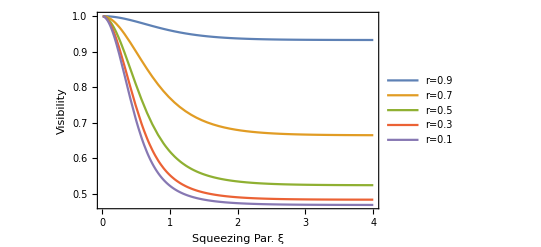

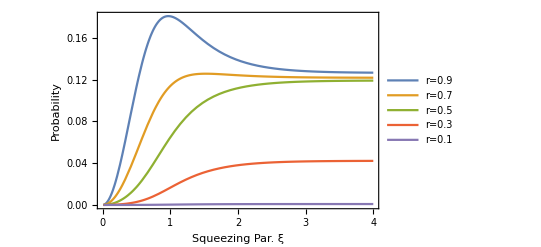

```mathematica
Plot[{Vwo2[0.9,ξ],Vwo2[0.7,ξ],Vwo2[0.5,ξ],Vwo2[0.32,ξ],Vwo2[0.1,ξ]},{ξ,0.01,4},PlotRange->Full,Frame->True,GridLines->{ {},{}},FrameLabel->{"Squeezing Par. ξ","Visibility","Vis. w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,ImageSize->Scaled[0.25]]
Plot[{wopostselect2[0,0.9,ξ],wopostselect2 [0,0.7,ξ],wopostselect2[0,0.5,ξ],wopostselect2[0,0.3,ξ],wopostselect2[0,0.1,ξ]},{ξ,0.01,4},PlotRange->{0,Full},Frame->True,FrameLabel->{"Squeezing Par. ξ","Probability","Max Prob. of Success w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,GridLines-> {{},{}},ImageSize->Scaled[0.30]]
```

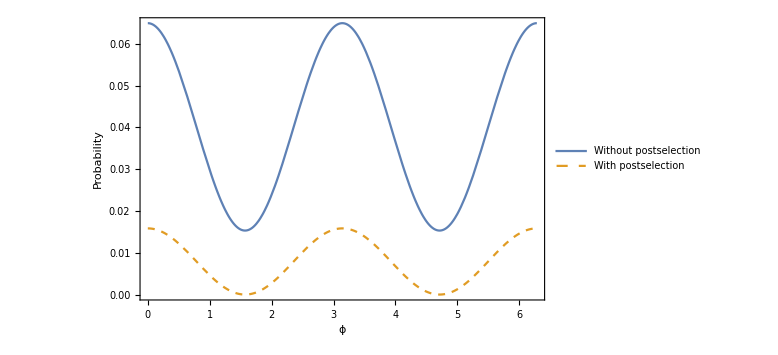

```mathematica
ClearAll[𝓇,ξ]
𝓇=0.5;
ξ=1;
Plot[{wopostselect2[ϕ,𝓇,ξ],wpostselect2[ϕ,𝓇,ξ]},{ϕ,0,2π},FrameLabel-> {"ϕ","Probability","Visibility (w/o , w ) postselection = ("<>ToString[Vwo2[𝓇,ξ]]<>" , "<>ToString[Vw2[𝓇,ξ]]<>")"},Frame-> True,PlotLegends->{"Without postselection","With postselection"},PlotStyle-> {Solid,Dashed},PlotRange->{0,Automatic},Ticks->{{0,π/2,π,(3π)/2,2π},Automatic},ImageSize->Large,LabelStyle->Large]
ClearAll[𝓇,ξ]
```

## 3. Two-Mode Squeezed Vacuum Input and observing interference for P(coincidence w/o PNR) = P(not 0,not 0) = P(any,any)-P(0,any)-P(any,0)+P(0,0)

```mathematica
ClearAll[out4,n]
n=5;
outcoin[ca2_,cb3_]=1/Cosh[ξ] Sum[(-Tanh[ξ]/1 ca0 cb0)^k/k!,{k,0,n}];
Prob[n_,ξ_]=Sech[ξ]^2(1-Tanh[ξ]^(2(n+1)))/(1-Tanh[ξ]^2);
(* Approximation of taking only a few terms *)
ClearAll[wopscoin,wpscoin,a,b,c,d]
a=0;  (* postselection on mode a *)
b=0;  (* postselection on mode b *)
(*c=1; (* amplitude for mode c chosen to observe the interference  *)
d=1;(* amplitude for mode d chosen to observe the interference  *)*)
wopscoin[ϕ_,𝓇_,ξ_]=Module[{ψp,ψ,P},
𝓉=√(1-𝓇^2);
(*ψp=CoefficientList[out4[ca,cb],{cc3,cd3}];*)
ψp=CoefficientList[outcoin[ca,cb],{cc3,cd3,ca,cb}];
ψ =Table[√((k-1)!(l-1)!)ψp[[k,l]],{k,1,Dimensions[ψp][[1]]},{l,1,Dimensions[ψp][[2]]}];
P=Table[Total[Total[Table[Abs[√((i-1)!(j-1)!)ψ[[k,l]][[i,j]]]^2,{i,1,Dimensions[ψ[[k,l]]][[1]]},{j,1,Dimensions[ψ[[k,l]]][[2]]}]]],{k,1,Dimensions[ψ][[1]]},{l,1,Dimensions[ψ][[2]]}];
(Total[Total[P]]-Total[P,{1}][[1]]-Total[P,{2}][[1]]+P[[1,1]])/Prob[n,ξ]
];
```

```mathematica
wpscoin[ϕ_,𝓇_,ξ_]=Module[{ψp,ψ,P},
𝓉=√(1-𝓇^2);
ψp=CoefficientList[outcoin[ca,cb],{cc3,cd3,ca,cb}];
ψ =Table[√((k-1)!(l-1)!)ψp[[k,l]],{k,1,Dimensions[ψp][[1]]},{l,1,Dimensions[ψp][[2]]}];
P=Table[Abs[√(a!b!)ψ[[k,l]][[a+1,b+1]]]^2,{k,1,Dimensions[ψ][[1]]},{l,1,Dimensions[ψ][[2]]}];
(Total[Total[P]]-Total[P,{1}][[1]]-Total[P,{2}][[1]]+P[[1,1]])/Prob[n,ξ]
];
(* Visibility *)
Vwocoin[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=wopscoin [0,𝓇,ξ];
Imin =wopscoin [Pi/2,𝓇,ξ];
N[(Imax-Imin)/(Imax+ Imin)]
];
Vwcoin[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=wpscoin [0,𝓇,ξ];
Imin =wpscoin [Pi/2,𝓇,ξ];
N[(Imax-Imin)/(Imax+ Imin)]
];
```

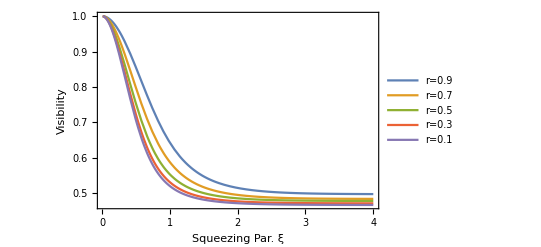

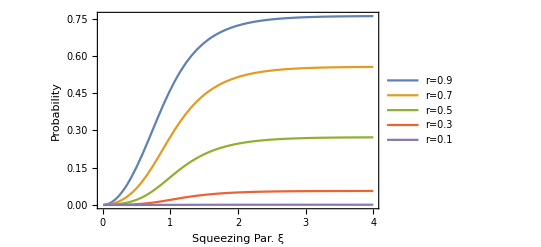

```mathematica
Plot[{Vwocoin[0.9,ξ],Vwocoin[0.7,ξ],Vwocoin[0.5,ξ],Vwocoin[0.3,ξ],Vwocoin[0.1,ξ]},{ξ,0.01,4},PlotRange->Full,GridLines->{{},{}},Frame->True,FrameLabel->{"Squeezing Par. ξ","Visibility","Vis. w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,ImageSize->Scaled[0.25]]
Plot[{wopscoin[0,0.9,ξ],wopscoin [0,0.7,ξ],wopscoin[0,0.5,ξ],wopscoin[0,0.3,ξ],wopscoin[0,0.1,ξ]},{ξ,0.01,4},PlotRange->{0,Full},Frame->True,FrameLabel->{"Squeezing Par. ξ","Probability","Max Prob. of Success w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},GridLines->{{},{}},LabelStyle->Large,ImageSize->Scaled[0.30]]
```

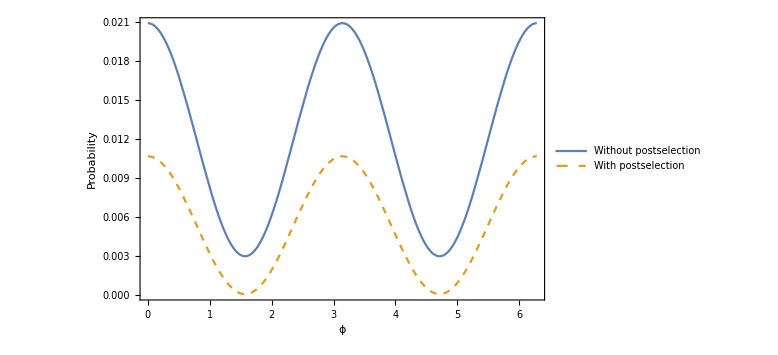

```mathematica
ClearAll[𝓇,ξ]
𝓇=0.5;
ξ=0.5;
Plot[{wopscoin[ϕ,𝓇,ξ],wpscoin[ϕ,𝓇,ξ]},{ϕ,0,2π},FrameLabel-> {"ϕ","Probability","Visibility (w/o , w ) postselection = ("<>ToString[Vwocoin[𝓇,ξ]]<>" , "<>ToString[Vwcoin[𝓇,ξ]]<>")"},Frame-> True,PlotLegends->{"Without postselection","With postselection"},PlotStyle-> {Solid,Dashed},PlotRange->{0,Automatic},Ticks->{{0,π/2,π,(3π)/2,2π},Automatic},ImageSize->Large,LabelStyle->Large]
ClearAll[𝓇,ξ]
```

## Attenuators in the upper arm only

```mathematica
ClearAll[B,ca0,ca1,ca2,cb0,cb1,cb2,cb3,cc1,cc2,cc3,cd1,cd2,cd3]
```

## Setup

#### Beam splitter transformation

```mathematica
B[r_,t_]={{t,-r},{r,t}};
```

```mathematica
(* Creation operators are representated by c *)
```

#### First beam splitter

```mathematica
{ca0,cb0}=B[1/(√2),1/(√2)].{ca1,cb1};
```

#### Phase shift in lower path

```mathematica
cb1=ⅇ^(-ⅈ ϕ)cb2;
```

#### Second and ‘Fourth’ beam splitters

```mathematica
{ca1,cc1}=B[𝓇,𝓉].{ca2,cc2};
{cb2,cd1}=B[1,0].{cb3,cd2};
(* Fourth beamsplitter has been turned into a mirror*)
```

#### Third beam splitter

```mathematica
{cc2,cd2}=B[1/(√2),1/(√2)].{cc3,cd3};
```

## 1. Single-Mode Squeezed Vacuum

### SMSV in mode a

```mathematica
ClearAll[S,out]
S[ξ_,n_]=1/(√Cosh[ξ])∑_(k=0)^n √Binomial[2k,k](-Tanh[ξ]/2)^k ca0^(2k)/(√((2k)!)); (* Source: Wikipedia*)
(* S[ξ,n] approximates single mode squeezed vacuum up to photon number = 2n *)
out[ca2_,cb3_,n_]=S[ξ,n];
Prob[n_,ξ_]=Sech[ξ]∑_(k=0)^n Binomial[2k,k](Tanh[ξ]/2)^(2k);
```

### Observing interference with and without postselection on modes a and b

#### c=1,d=1

```mathematica
ClearAll[n,a,b,c,d,wopostselect,wpostselect]
n=5;  (* Squeezed states approximated with 2n terms *)
a=0;  (* postselection on mode a *)
b=0;  (* postselection on mode b *)
c=1; (* amplitude for mode c chosen to observe the interference  *)
d=1;(* amplitude for mode d chosen to observe the interference  *)
wopostselect[ϕ_,𝓇_,ξ_] = Module[{coeffψ,coefftable},
𝓉=√(1-𝓇^2);
coeffψ =√(c!d!)CoefficientList[CoefficientList[out[ca,cb,n],{cc3,cd3}][[c+1,d+1]],{ca,cb}];
coefftable=Table[Abs[√((i-1)!   (j-1)!)coeffψ[[i,j]]]^2,{i,1,Dimensions[coeffψ][[1]]},{j,1,Dimensions[coeffψ][[2]]}];
Total[Total[coefftable]]/Prob[n,ξ]
];
wpostselect[ϕ_,𝓇_,ξ_]=Module[{},
𝓉=√(1-𝓇^2);
Abs[√(c!d! a!b!)CoefficientList[CoefficientList[out[ca,cb,n],{cc3,cd3}][[c+1,d+1]],{ca,cb}][[a+1,b+1]]]^2/Prob[n,ξ]
];
Vwo[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=FindMaximum[wopostselect [x,𝓇,ξ],{x,3 π/4}][[1]];
Imin = FindMinimum[wopostselect [x,𝓇,ξ],{x,3 π/4}][[1]];
N[(Imax-Imin)/(Imax+ Imin)]
];
Vw[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=FindMaximum[wpostselect[x,𝓇,ξ],{x,3 π/4}][[1]];
Imin = FindMinimum[wpostselect [x,𝓇,ξ],{x,3 π/4}][[1]];
N[(Imax-Imin)/(Imax+ Imin)]
];
(*Manipulate[Plot[{wopostselect [ϕ,𝓇,ξ],wpostselect[ϕ,𝓇,ξ]},{ϕ,0,2π},PlotLabel-> "Visibility (w/o , w ) postselection = ("<>ToString[Vwo[𝓇,ξ]]<>" , "<>ToString[Vw[𝓇,ξ]]<>")",AxesLabel-> {ϕ,P},PlotLegends->{"Without postselection","With postselection"},Ticks->{{0,π/2,π,(3π)/2,2π},Automatic},PlotStyle-> {Solid,Dashed},PlotRange->Full,ImageSize->Medium],{ξ,5,10,Appearance-> "Open"},{𝓇,0.1,1,Appearance-> "Open"}]*)
```

```mathematica
FindMaximum[{wopostselect[π/2,𝓇,ξ],0≤𝓇≤1&&0<ξ},{𝓇,0.5},{ξ,1}]
```

{0.100669,{𝓇→1.,ξ→1.33327}}

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

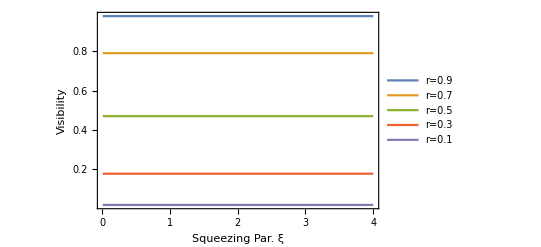

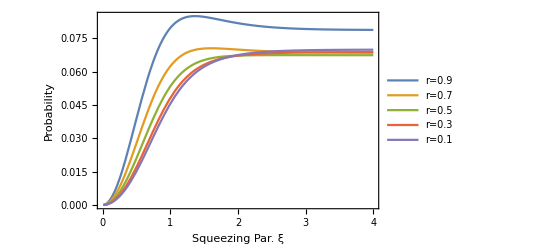

```mathematica
ClearAll[𝓇,ξ]
Plot[{Vwo[0.9,ξ],Vwo[0.7,ξ],Vwo[0.5,ξ],Vwo[0.3,ξ],Vwo[0.1,ξ]},{ξ,0.01,4},PlotRange->Full,Frame->True,FrameLabel->{"Squeezing Par. ξ","Visibility","Vis. w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,ImageSize->Scaled[0.25]]
Plot[{wopostselect[π/2,0.9,ξ],wopostselect[π/2,0.7,ξ],wopostselect[π/2,0.5,ξ],wopostselect[π/2,0.3,ξ],wopostselect[π/2,0.1,ξ]},{ξ,0.01,4},PlotRange->{0,Full},Frame->True,FrameLabel->{"Squeezing Par. ξ","Probability","Max Prob. of Success w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,ImageSize->Scaled[0.30]]
ClearAll[𝓇,ξ]
```

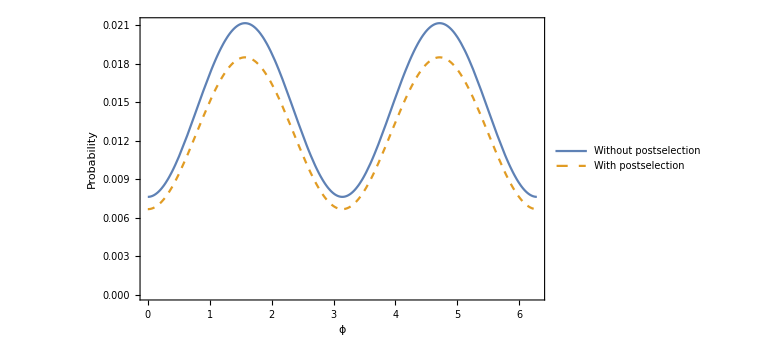

```mathematica
𝓇=0.5;
ξ=0.5;
Plot[{wopostselect[ϕ,𝓇,ξ],wpostselect[ϕ,𝓇,ξ]},{ϕ,0,2π},FrameLabel-> {"ϕ","Probability","Visibility (w/o , w ) postselection = ("<>ToString[Vwo[𝓇,ξ]]<>" , "<>ToString[Vw[𝓇,ξ]]<>") for 𝓇=0.5, ξ=1.462"},Frame-> True,PlotLegends->{"Without postselection","With postselection"},PlotStyle-> {Solid,Dashed},PlotRange->{0,Automatic},Ticks->{{0,π/2,π,(3π)/2,2π},Automatic},ImageSize->Large,LabelStyle->Large]
ClearAll[𝓇,ξ]
```

#### c=2,d=2

```mathematica
ClearAll[n,a,b,c,d,wopostselect,wpostselect]
n=10;  (* Squeezed states approximated with 2n terms *)
a=0;  (* postselection on mode a *)
b=0;  (* postselection on mode b *)
c=2; (* amplitude for mode c chosen to observe the interference  *)
d=2;(* amplitude for mode d chosen to observe the interference  *)
Prob[n_,ξ_]=Sech[ξ]∑_(k=0)^n Binomial[2k,k](Tanh[ξ]/2)^(2k);
wopostselect[ϕ_,𝓇_,ξ_] = Module[{coeffψ,coefftable},
𝓉=√(1-𝓇^2);
coeffψ =√(c!d!)CoefficientList[CoefficientList[out[ca,cb,n],{cc3,cd3}][[c+1,d+1]],{ca,cb}];
coefftable=Table[Abs[√((i-1)!   (j-1)!)coeffψ[[i,j]]]^2,{i,1,Dimensions[coeffψ][[1]]},{j,1,Dimensions[coeffψ][[2]]}];
Total[Total[coefftable]]/Prob[n,ξ]
];
wpostselect[ϕ_,𝓇_,ξ_]=Module[{},
𝓉=√(1-𝓇^2);
Abs[√(c!d! a!b!)CoefficientList[CoefficientList[out[ca,cb,n],{cc3,cd3}][[c+1,d+1]],{ca,cb}][[a+1,b+1]]]^2/Prob[n,ξ]
];
Vwo[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=FindMaximum[wopostselect [x,𝓇,ξ],{x,3 π/4}][[1]];
Imin = FindMinimum[wopostselect [x,𝓇,ξ],{x,3 π/4}][[1]];
N[(Imax-Imin)/(Imax+ Imin)]
];
Vw[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=FindMaximum[wpostselect[x,𝓇,ξ],{x,3 π/4}][[1]];
Imin = FindMinimum[wpostselect [x,𝓇,ξ],{x,3 π/4}][[1]];
N[(Imax-Imin)/(Imax+ Imin)]
];
(*Manipulate[Plot[{wopostselect [ϕ,𝓇,ξ],wpostselect[ϕ,𝓇,ξ]},{ϕ,0,2π},PlotLabel-> "Visibility (w/o , w ) postselection = ("<>ToString[Vwo[𝓇,ξ]]<>" , "<>ToString[Vw[𝓇,ξ]]<>")",AxesLabel-> {ϕ,P},PlotLegends->{"Without postselection","With postselection"},Ticks->{{0,π/2,π,(3π)/2,2π},Automatic},PlotStyle-> {Solid,Dashed},PlotRange->Full,ImageSize->Medium],{ξ,5,10,Appearance-> "Open"},{𝓇,0.1,1,Appearance-> "Open"}]*)
```

{0.0419302,{𝓇→0.999999,ξ→1.61082}}

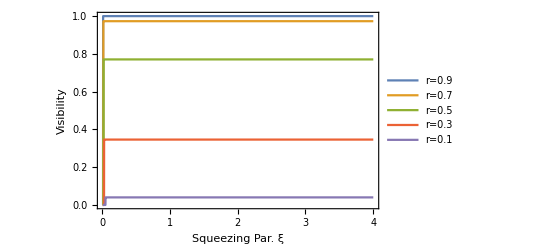

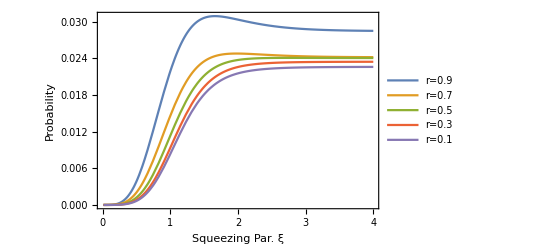

```mathematica
ClearAll[𝓇,ξ]
FindMaximum[{wopostselect[π/2,𝓇,ξ],0≤𝓇≤1&&0<ξ},{𝓇,0.5},{ξ,1}]
Plot[{Vwo[0.9,ξ],Vwo[0.7,ξ],Vwo[0.5,ξ],Vwo[0.3,ξ],Vwo[0.1,ξ]},{ξ,0.01,4},PlotRange->Full,Frame->True,FrameLabel->{"Squeezing Par. ξ","Visibility","Vis. w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,ImageSize->Scaled[0.25]]
Plot[{wopostselect[π/2,0.9,ξ],wopostselect[π/2,0.7,ξ],wopostselect[π/2,0.5,ξ],wopostselect[π/2,0.3,ξ],wopostselect[π/2,0.1,ξ]},{ξ,0.01,4},PlotRange->{0,Full},Frame->True,FrameLabel->{"Squeezing Par. ξ","Probability","Max Prob. of Success w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,ImageSize->Scaled[0.30]]
ClearAll[𝓇,ξ]
```

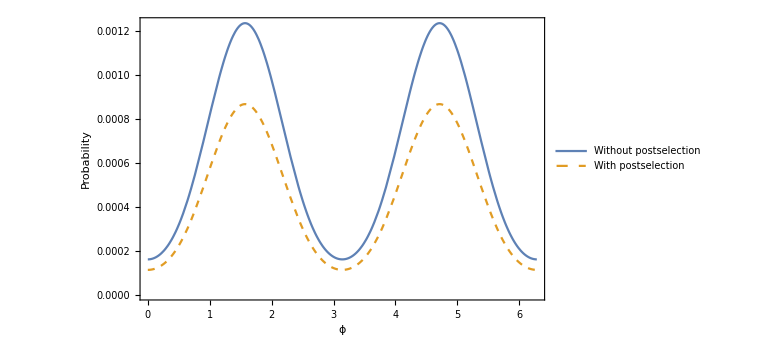

```mathematica
ClearAll[𝓇,ξ]
𝓇=0.5;
ξ=0.5;
Plot[{wopostselect[ϕ,𝓇,ξ],wpostselect[ϕ,𝓇,ξ]},{ϕ,0,2π},FrameLabel-> {"ϕ","Probability","Visibility (w/o , w ) postselection = ("<>ToString[Vwo[𝓇,ξ]]<>" , "<>ToString[Vw[𝓇,ξ]]<>") for 𝓇=0.5, ξ=1.462"},Frame-> True,PlotLegends->{"Without postselection","With postselection"},PlotStyle-> {Solid,Dashed},PlotRange->{0,Automatic},Ticks->{{0,π/2,π,(3π)/2,2π},Automatic},ImageSize->Large,LabelStyle->Large]
ClearAll[𝓇,ξ]
```

## 2. Two-Mode Squeezed Vacuum Input and observing interference for P(1,1)

```mathematica
(* T[ξ_,n_]=1/Cosh[ξ]∑_(k=0)^n (-Tanh[ξ]/1)^k(ca0^k cb0^k)/(k!); (* Source: Wikipedia*)*)
(* T[ξ,n] approximates two mode squeezed vacuum up to photon number = n,n *)
ClearAll[out2,n]
n=5;
out2[ca2_,cb3_]=1/Cosh[ξ] Sum[(-Tanh[ξ]/1 ca0 cb0)^k/k!,{k,0,n}];
Prob[n_,ξ_]=Sech[ξ]^2(1-Tanh[ξ]^(2(n+1)))/(1-Tanh[ξ]^2);
```

```mathematica
(* Approximation of taking only a few terms *)
```

```mathematica
ClearAll[a,b,c,d,wopostselect2,wpostselect2]
a=0;  (* postselection on mode a *)
b=0;  (* postselection on mode b *)
c=1; (* amplitude for mode c chosen to observe the interference  *)
d=1;(* amplitude for mode d chosen to observe the interference  *)
wopostselect2[ϕ_,𝓇_,ξ_] = Module[{coeffψ,coefftable},
𝓉=√(1-𝓇^2);
coeffψ =√(c!d!)CoefficientList[CoefficientList[out2[ca,cb],{cc3,cd3}][[c+1,d+1]],{ca,cb}];
coefftable=Table[Abs[√((i-1)!   (j-1)!)coeffψ[[i,j]]]^2,{i,1,Dimensions[coeffψ][[1]]},{j,1,Dimensions[coeffψ][[2]]}];
Total[Total[coefftable]]/Prob[n,ξ]
];
wpostselect2[ϕ_,𝓇_,ξ_]=Module[{},
𝓉=√(1-𝓇^2);
Abs[√(c!d! a!b!)CoefficientList[CoefficientList[out2[ca,cb],{cc3,cd3}][[c+1,d+1]],{ca,cb}][[a+1,b+1]]]^2/Prob[n,ξ]
];
(* Visibility *)
Vwo2[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=wopostselect2 [0,𝓇,ξ];
Imin =wopostselect2 [Pi/2,𝓇,ξ];
N[(Imax-Imin)/(Imax+ Imin)]
];
Vw2[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=wpostselect2 [0,𝓇,ξ];
Imin =wpostselect2 [Pi/2,𝓇,ξ];
N[(Imax-Imin)/(Imax+ Imin)]
];
```

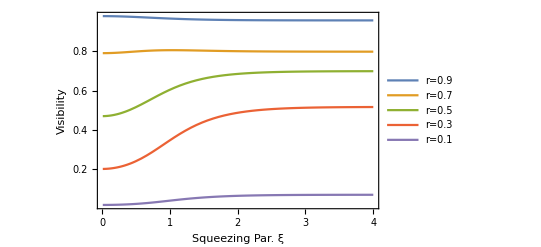

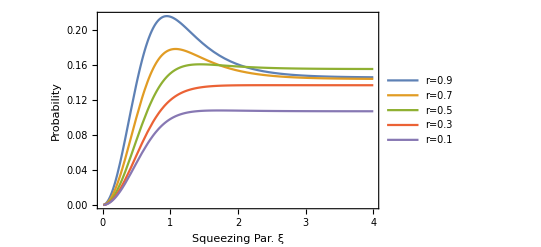

```mathematica
Plot[{Vwo2[0.9,ξ],Vwo2[0.7,ξ],Vwo2[0.5,ξ],Vwo2[0.32,ξ],Vwo2[0.1,ξ]},{ξ,0.01,4},PlotRange->Full,Frame->True,GridLines->{ {},{}},FrameLabel->{"Squeezing Par. ξ","Visibility","Vis. w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,ImageSize->Scaled[0.25]]
Plot[{wopostselect2[0,0.9,ξ],wopostselect2 [0,0.7,ξ],wopostselect2[0,0.5,ξ],wopostselect2[0,0.3,ξ],wopostselect2[0,0.1,ξ]},{ξ,0.01,4},PlotRange->{0,Full},Frame->True,FrameLabel->{"Squeezing Par. ξ","Probability","Max Prob. of Success w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,GridLines-> {{},{}},ImageSize->Scaled[0.30]]
```

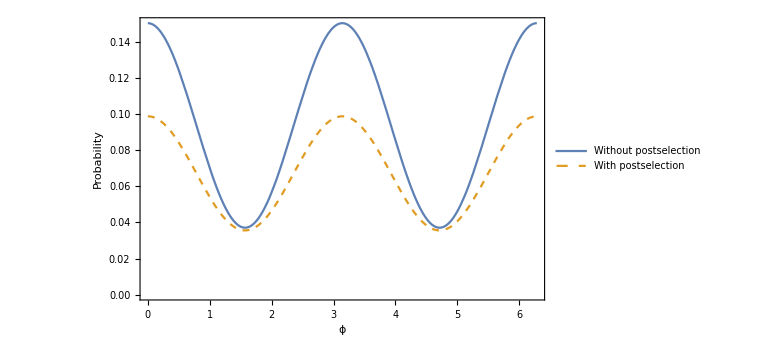

```mathematica
ClearAll[𝓇,ξ]
𝓇=0.5;
ξ=1;
Plot[{wopostselect2[ϕ,𝓇,ξ],wpostselect2[ϕ,𝓇,ξ]},{ϕ,0,2π},FrameLabel-> {"ϕ","Probability","Visibility (w/o , w ) postselection = ("<>ToString[Vwo2[𝓇,ξ]]<>" , "<>ToString[Vw2[𝓇,ξ]]<>")"},Frame-> True,PlotLegends->{"Without postselection","With postselection"},PlotStyle-> {Solid,Dashed},PlotRange->{0,Automatic},Ticks->{{0,π/2,π,(3π)/2,2π},Automatic},ImageSize->Large,LabelStyle->Large]
ClearAll[𝓇,ξ]
```

## 3. Two-Mode Squeezed Vacuum Input and observing interference for P(coincidence w/o PNR) = P(not 0,not 0) = P(any,any)-P(0,any)-P(any,0)+P(0,0)

```mathematica
ClearAll[out4,n]
n=5;
outcoin[ca2_,cb3_]=1/Cosh[ξ] Sum[(-Tanh[ξ]/1 ca0 cb0)^k/k!,{k,0,n}];
Prob[n_,ξ_]=Sech[ξ]^2(1-Tanh[ξ]^(2(n+1)))/(1-Tanh[ξ]^2);
(* Approximation of taking only a few terms *)
ClearAll[wopscoin,wpscoin,a,b,c,d]
a=0;  (* postselection on mode a *)
b=0;  (* postselection on mode b *)
(*c=1; (* amplitude for mode c chosen to observe the interference  *)
d=1;(* amplitude for mode d chosen to observe the interference  *)*)
wopscoin[ϕ_,𝓇_,ξ_]=Module[{ψp,ψ,P},
𝓉=√(1-𝓇^2);
(*ψp=CoefficientList[out4[ca,cb],{cc3,cd3}];*)
ψp=CoefficientList[outcoin[ca,cb],{cc3,cd3,ca,cb}];
ψ =Table[√((k-1)!(l-1)!)ψp[[k,l]],{k,1,Dimensions[ψp][[1]]},{l,1,Dimensions[ψp][[2]]}];
P=Table[Total[Total[Table[Abs[√((i-1)!(j-1)!)ψ[[k,l]][[i,j]]]^2,{i,1,Dimensions[ψ[[k,l]]][[1]]},{j,1,Dimensions[ψ[[k,l]]][[2]]}]]],{k,1,Dimensions[ψ][[1]]},{l,1,Dimensions[ψ][[2]]}];
(Total[Total[P]]-Total[P,{1}][[1]]-Total[P,{2}][[1]]+P[[1,1]])/Prob[n,ξ]
];
```

```mathematica
wpscoin[ϕ_,𝓇_,ξ_]=Module[{ψp,ψ,P},
𝓉=√(1-𝓇^2);
ψp=CoefficientList[outcoin[ca,cb],{cc3,cd3,ca,cb}];
ψ =Table[√((k-1)!(l-1)!)ψp[[k,l]],{k,1,Dimensions[ψp][[1]]},{l,1,Dimensions[ψp][[2]]}];
P=Table[Abs[√(a!b!)ψ[[k,l]][[a+1,b+1]]]^2,{k,1,Dimensions[ψ][[1]]},{l,1,Dimensions[ψ][[2]]}];
(Total[Total[P]]-Total[P,{1}][[1]]-Total[P,{2}][[1]]+P[[1,1]])/Prob[n,ξ]
];
(* Visibility *)
Vwocoin[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=wopscoin [0,𝓇,ξ];
Imin =wopscoin [Pi/2,𝓇,ξ];
N[(Imax-Imin)/(Imax+ Imin)]
];
Vwcoin[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=wpscoin [0,𝓇,ξ];
Imin =wpscoin [Pi/2,𝓇,ξ];
N[(Imax-Imin)/(Imax+ Imin)]
];
```

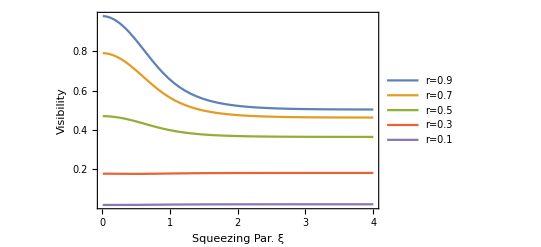

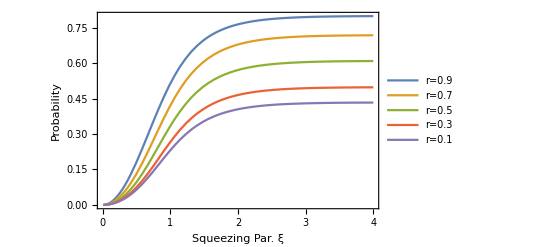

```mathematica
Plot[{Vwocoin[0.9,ξ],Vwocoin[0.7,ξ],Vwocoin[0.5,ξ],Vwocoin[0.3,ξ],Vwocoin[0.1,ξ]},{ξ,0.01,4},PlotRange->Full,GridLines->{{},{}},Frame->True,FrameLabel->{"Squeezing Par. ξ","Visibility","Vis. w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,ImageSize->Scaled[0.25]]
Plot[{wopscoin[0,0.9,ξ],wopscoin [0,0.7,ξ],wopscoin[0,0.5,ξ],wopscoin[0,0.3,ξ],wopscoin[0,0.1,ξ]},{ξ,0.01,4},PlotRange->{0,Full},Frame->True,FrameLabel->{"Squeezing Par. ξ","Probability","Max Prob. of Success w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},GridLines->{{},{}},LabelStyle->Large,ImageSize->Scaled[0.30]]
```

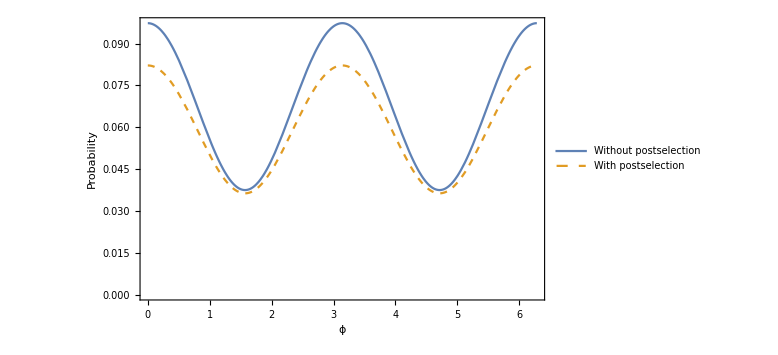

```mathematica
ClearAll[𝓇,ξ]
𝓇=0.5;
ξ=0.5;
Plot[{wopscoin[ϕ,𝓇,ξ],wpscoin[ϕ,𝓇,ξ]},{ϕ,0,2π},FrameLabel-> {"ϕ","Probability","Visibility (w/o , w ) postselection = ("<>ToString[Vwocoin[𝓇,ξ]]<>" , "<>ToString[Vwcoin[𝓇,ξ]]<>")"},Frame-> True,PlotLegends->{"Without postselection","With postselection"},PlotStyle-> {Solid,Dashed},PlotRange->{0,Automatic},Ticks->{{0,π/2,π,(3π)/2,2π},Automatic},ImageSize->Large,LabelStyle->Large]
ClearAll[𝓇,ξ]
```

## Attenuators in both the arms of Mach-Zehnder (inefficient detectors)

## Setup

#### Beam splitter transformation

```mathematica
B[r_,t_]={{t,-r},{r,t}};
```

```mathematica
(* Creation operators are representated by c *)
```

#### First beam splitter

```mathematica
{ca0,cb0}=B[1/(√2),1/(√2)].{ca1,cb1};
```

#### Phase shift in lower path

```mathematica
cb1=ⅇ^(-ⅈ ϕ)cb2;
```

#### Second and ‘Fourth’ beam splitters

```mathematica
{ca1,cc1}=B[𝓇,𝓉].{ca2p,cc2};
{cb2,cd1}=B[𝓇,𝓉].{cb3p,cd2};
```

#### Fifth and Sixth beam splitters (to simulate inefficient detectors in modes a and b)

```mathematica
{ca2p,cadumpp}=B[𝓇loss,𝓉loss].{ca2,cadump};
{cb3p,cbdumpp}=B[𝓇loss,𝓉loss].{cb3,cbdump};
```

#### Third beam splitter

```mathematica
{cc2,cd2}=B[1/(√2),1/(√2)].{cc3,cd3};
```

```mathematica
𝓇loss=√(0.10/2);(*10% total loss of photons in both detectors, due to inefficiency *)
𝓉loss=√(1-𝓇loss^2);
```

## 1. Single-Mode Squeezed Vacuum

### SMSV in mode a

```mathematica
ClearAll[S,out]
S[ξ_,n_]=1/(√Cosh[ξ])∑_(k=0)^n √Binomial[2k,k](-Tanh[ξ]/2)^k ca0^(2k)/(√((2k)!)); (* Source: Wikipedia*)
(* S[ξ,n] approximates single mode squeezed vacuum up to photon number = 2n *)
out[ca2_,cb3_,n_]=S[ξ,n];
Prob[n_,ξ_]=Sech[ξ]∑_(k=0)^n Binomial[2k,k](Tanh[ξ]/2)^(2k);
```

### Observing interference with and without postselection on modes a and b

#### c=1,d=1

```mathematica
ClearAll[n,a,b,c,d,wopostselect,wpostselect]
n=5;  (* Squeezed states approximated with 2n terms *)
a=0;  (* postselection on mode a *)
b=0;  (* postselection on mode b *)
c=1; (* amplitude for mode c chosen to observe the interference  *)
d=1;(* amplitude for mode d chosen to observe the interference  *)

wopostselect[ϕ_,𝓇_,ξ_] = Module[{ψ,P},
𝓉=√(1-𝓇^2);
ψ =√(c!d!)CoefficientList[CoefficientList[out[ca,cb,n],{cc3,cd3}][[c+1,d+1]],{ca,cb,cadump,cbdump}];
P=Table[Abs[√((i-1)!   (j-1)!(k-1)!(l-1)!)ψ[[i,j,k,l]]]^2,{i,1,Dimensions[ψ][[1]]},{j,1,Dimensions[ψ][[2]]},{k,1,Dimensions[ψ][[3]]},{l,1,Dimensions[ψ][[4]]}];
Total[P,4]/Prob[n,ξ]
];
wpostselect[ϕ_,𝓇_,ξ_]=Module[{ψ,P},
𝓉=√(1-𝓇^2);
ψ=√(c!d! a!b!)CoefficientList[out[ca,cb,n],{cc3,cd3,ca,cb,cadump,cbdump}][[c+1,d+1,a+1,b+1]];
P=Table[Abs[√((k-1)!(l-1)!)ψ[[k,l]]]^2,{k,1,Dimensions[ψ][[1]]},{l,1,Dimensions[ψ][[2]]}];
Total[P,2]/Prob[n,ξ]
];
Vwo[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=FindMaximum[wopostselect [x,𝓇,ξ],{x,3 π/4}][[1]];
Imin = FindMinimum[wopostselect [x,𝓇,ξ],{x,3 π/4}][[1]];
N[(Imax-Imin)/(Imax+ Imin)]
];
Vw[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=FindMaximum[wpostselect[x,𝓇,ξ],{x,3 π/4}][[1]];
Imin = FindMinimum[wpostselect [x,𝓇,ξ],{x,3 π/4}][[1]];
N[(Imax-Imin)/(Imax+ Imin)]
];
```

```mathematica
ClearAll[𝓇,ξ]
Plot[{Vwo[0.9,ξ],Vwo[0.7,ξ],Vwo[0.5,ξ],Vwo[0.3,ξ],Vwo[0.1,ξ]},{ξ,0.01,4},PlotRange->Full,Frame->True,FrameLabel->{"Squeezing Par. ξ","Visibility","Vis. w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,ImageSize->Scaled[0.25]]
Plot[{wopostselect[π/2,0.9,ξ],wopostselect[π/2,0.7,ξ],wopostselect[π/2,0.5,ξ],wopostselect[π/2,0.3,ξ],wopostselect[π/2,0.1,ξ]},{ξ,0.01,4},PlotRange->{0,Full},Frame->True,FrameLabel->{"Squeezing Par. ξ","Probability","Max Prob. of Success w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,ImageSize->Scaled[0.30]]
ClearAll[𝓇,ξ]
```

-Graphics-

-Graphics-

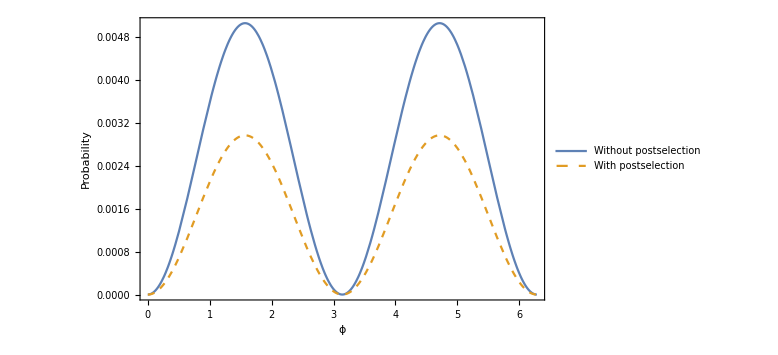

```mathematica
𝓇=0.5;
ξ=0.5;
Plot[{wopostselect[ϕ,𝓇,ξ],wpostselect[ϕ,𝓇,ξ]},{ϕ,0,2π},FrameLabel-> {"ϕ","Probability","Visibility (w/o , w ) postselection = ("<>ToString[Vwo[𝓇,ξ]]<>" , "<>ToString[Vw[𝓇,ξ]]<>") for 𝓇=0.5, ξ=1.462"},Frame-> True,PlotLegends->{"Without postselection","With postselection"},PlotStyle-> {Solid,Dashed},PlotRange->{0,Automatic},Ticks->{{0,π/2,π,(3π)/2,2π},Automatic},ImageSize->Large,LabelStyle->Large]
ClearAll[𝓇,ξ]
```

#### c=2,d=2

```mathematica
ClearAll[n,a,b,c,d,wopostselect,wpostselect]
n=10;  (* Squeezed states approximated with 2n terms *)
a=0;  (* postselection on mode a *)
b=0;  (* postselection on mode b *)
c=2; (* amplitude for mode c chosen to observe the interference  *)
d=2;(* amplitude for mode d chosen to observe the interference  *)
wopostselect[ϕ_,𝓇_,ξ_] = Module[{ψ,P},
𝓉=√(1-𝓇^2);
ψ =√(c!d!)CoefficientList[CoefficientList[out[ca,cb,n],{cc3,cd3}][[c+1,d+1]],{ca,cb,cadump,cbdump}];
P=Table[Abs[√((i-1)!   (j-1)!(k-1)!(l-1)!)ψ[[i,j,k,l]]]^2,{i,1,Dimensions[ψ][[1]]},{j,1,Dimensions[ψ][[2]]},{k,1,Dimensions[ψ][[3]]},{l,1,Dimensions[ψ][[4]]}];
Total[P,4]/Prob[n,ξ]
];
wpostselect[ϕ_,𝓇_,ξ_]=Module[{ψ,P},
𝓉=√(1-𝓇^2);
ψ=√(c!d! a!b!)CoefficientList[out[ca,cb,n],{cc3,cd3,ca,cb,cadump,cbdump}][[c+1,d+1,a+1,b+1]];
P=Table[Abs[√((k-1)!(l-1)!)ψ[[k,l]]]^2,{k,1,Dimensions[ψ][[1]]},{l,1,Dimensions[ψ][[2]]}];
Total[P,2]/Prob[n,ξ]
];
Vwo[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=FindMaximum[wopostselect [x,𝓇,ξ],{x,3 π/4}][[1]];
Imin = FindMinimum[wopostselect [x,𝓇,ξ],{x,3 π/4}][[1]];
N[(Imax-Imin)/(Imax+ Imin)]
];
Vw[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=FindMaximum[wpostselect[x,𝓇,ξ],{x,3 π/4}][[1]];
Imin = FindMinimum[wpostselect [x,𝓇,ξ],{x,3 π/4}][[1]];
N[(Imax-Imin)/(Imax+ Imin)]
];
(*Manipulate[Plot[{wopostselect [ϕ,𝓇,ξ],wpostselect[ϕ,𝓇,ξ]},{ϕ,0,2π},PlotLabel-> "Visibility (w/o , w ) postselection = ("<>ToString[Vwo[𝓇,ξ]]<>" , "<>ToString[Vw[𝓇,ξ]]<>")",AxesLabel-> {ϕ,P},PlotLegends->{"Without postselection","With postselection"},Ticks->{{0,π/2,π,(3π)/2,2π},Automatic},PlotStyle-> {Solid,Dashed},PlotRange->Full,ImageSize->Medium],{ξ,5,10,Appearance-> "Open"},{𝓇,0.1,1,Appearance-> "Open"}]*)
```

```mathematica
ClearAll[𝓇,ξ]
FindMaximum[{wopostselect[π/2,𝓇,ξ],0≤𝓇≤1&&0<ξ},{𝓇,0.5},{ξ,1}]
Plot[{Vwo[0.9,ξ],Vwo[0.7,ξ],Vwo[0.5,ξ],Vwo[0.3,ξ],Vwo[0.1,ξ]},{ξ,0.01,4},PlotRange->Full,Frame->True,FrameLabel->{"Squeezing Par. ξ","Visibility","Vis. w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,ImageSize->Scaled[0.25]]
Plot[{wopostselect[π/2,0.9,ξ],wopostselect[π/2,0.7,ξ],wopostselect[π/2,0.5,ξ],wopostselect[π/2,0.3,ξ],wopostselect[π/2,0.1,ξ]},{ξ,0.01,4},PlotRange->{0,Full},Frame->True,FrameLabel->{"Squeezing Par. ξ","Probability","Max Prob. of Success w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,ImageSize->Scaled[0.30]]
ClearAll[𝓇,ξ]
```

{0.0419302,{𝓇→1.,ξ→1.61082}}

FindMaximum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a maximum; it may be a minimum or a saddle point.

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

-Graphics-

-Graphics-

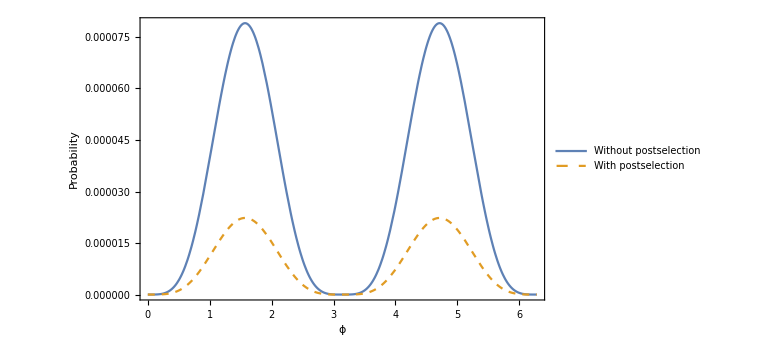

```mathematica
ClearAll[𝓇,ξ]
𝓇=0.5;
ξ=0.5;
Plot[{wopostselect[ϕ,𝓇,ξ],wpostselect[ϕ,𝓇,ξ]},{ϕ,0,2π},FrameLabel-> {"ϕ","Probability","Visibility (w/o , w ) postselection = ("<>ToString[Vwo[𝓇,ξ]]<>" , "<>ToString[Vw[𝓇,ξ]]<>") for 𝓇=0.5, ξ=1.462"},Frame-> True,PlotLegends->{"Without postselection","With postselection"},PlotStyle-> {Solid,Dashed},PlotRange->{0,Automatic},Ticks->{{0,π/2,π,(3π)/2,2π},Automatic},ImageSize->Large,LabelStyle->Large]
ClearAll[𝓇,ξ]
```

## 2. Two-Mode Squeezed Vacuum Input and observing interference for P(1,1)

```mathematica
(* T[ξ_,n_]=1/Cosh[ξ]∑_(k=0)^n (-Tanh[ξ]/1)^k(ca0^k cb0^k)/(k!); (* Source: Wikipedia*)*)
(* T[ξ,n] approximates two mode squeezed vacuum up to photon number = n,n *)
ClearAll[out2,n]
n=5;
out2[ca2_,cb3_]=1/Cosh[ξ] Sum[(-Tanh[ξ]/1 ca0 cb0)^k/k!,{k,0,n}];
Prob[n_,ξ_]=Sech[ξ]^2(1-Tanh[ξ]^(2(n+1)))/(1-Tanh[ξ]^2);
```

```mathematica
(* Approximation of taking only a few terms *)
```

```mathematica
ClearAll[a,b,c,d,wopostselect2,wpostselect2]
a=0;  (* postselection on mode a *)
b=0;  (* postselection on mode b *)
c=1; (* amplitude for mode c chosen to observe the interference  *)
d=1;(* amplitude for mode d chosen to observe the interference  *)

wopostselect2[ϕ_,𝓇_,ξ_] = Module[{ψ,P},
𝓉=√(1-𝓇^2);
ψ =√(c!d!)CoefficientList[out2[ca,cb],{cc3,cd3,ca,cb,cadump,cbdump}][[c+1,d+1]];
P=Table[Abs[√((i-1)!   (j-1)!(k-1)!(l-1)!)ψ[[i,j,k,l]]]^2,{i,1,Dimensions[ψ][[1]]},{j,1,Dimensions[ψ][[2]]},{k,1,Dimensions[ψ][[3]]},{l,1,Dimensions[ψ][[4]]}];
Total[P,4]/Prob[n,ξ]
];
wpostselect2[ϕ_,𝓇_,ξ_]=Module[{ψ,P},
𝓉=√(1-𝓇^2);
ψ=√(c!d! a!b!)CoefficientList[out2[ca,cb],{cc3,cd3,ca,cb,cadump,cbdump}][[c+1,d+1,a+1,b+1]];
P=Table[Abs[√((k-1)!(l-1)!)ψ[[k,l]]]^2,{k,1,Dimensions[ψ][[1]]},{l,1,Dimensions[ψ][[2]]}];
Total[P,2]/Prob[n,ξ]
];

(* Visibility *)
Vwo2[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=wopostselect2 [0,𝓇,ξ];
Imin =wopostselect2 [Pi/2,𝓇,ξ];
N[(Imax-Imin)/(Imax+ Imin)]
];
Vw2[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=wpostselect2 [0,𝓇,ξ];
Imin =wpostselect2 [Pi/2,𝓇,ξ];
N[(Imax-Imin)/(Imax+ Imin)]
];
```

```mathematica
Plot[{Vwo2[0.9,ξ],Vwo2[0.7,ξ],Vwo2[0.5,ξ],Vwo2[0.32,ξ],Vwo2[0.1,ξ]},{ξ,0.01,4},PlotRange->Full,Frame->True,GridLines->{ {},{}},FrameLabel->{"Squeezing Par. ξ","Visibility","Vis. w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,ImageSize->Scaled[0.25]]
Plot[{wopostselect2[0,0.9,ξ],wopostselect2 [0,0.7,ξ],wopostselect2[0,0.5,ξ],wopostselect2[0,0.3,ξ],wopostselect2[0,0.1,ξ]},{ξ,0.01,4},PlotRange->{0,Full},Frame->True,FrameLabel->{"Squeezing Par. ξ","Probability","Max Prob. of Success w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,GridLines-> {{},{}},ImageSize->Scaled[0.30]]
```

-Graphics-

-Graphics-

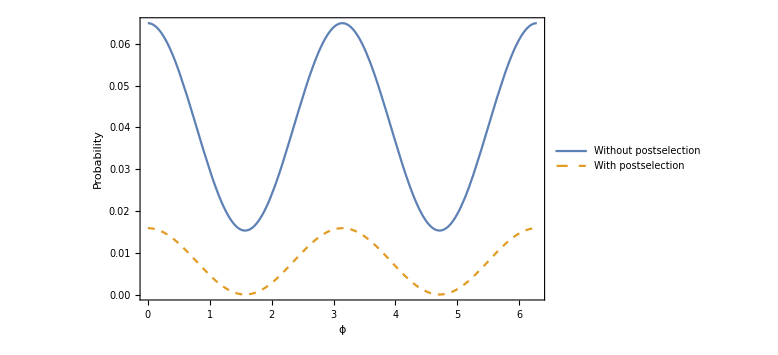

```mathematica
ClearAll[𝓇,ξ]
𝓇=0.5;
ξ=1;
Plot[{wopostselect2[ϕ,𝓇,ξ],wpostselect2[ϕ,𝓇,ξ]},{ϕ,0,2π},FrameLabel-> {"ϕ","Probability","Visibility (w/o , w ) postselection = ("<>ToString[Vwo2[𝓇,ξ]]<>" , "<>ToString[Vw2[𝓇,ξ]]<>")"},Frame-> True,PlotLegends->{"Without postselection","With postselection"},PlotStyle-> {Solid,Dashed},PlotRange->{0,Automatic},Ticks->{{0,π/2,π,(3π)/2,2π},Automatic},ImageSize->Large,LabelStyle->Large]
ClearAll[𝓇,ξ]
```

## 3. Two-Mode Squeezed Vacuum Input and observing interference for P(coincidence w/o PNR) = P(not 0,not 0) = P(any,any)-P(0,any)-P(any,0)+P(0,0)

```mathematica
ClearAll[outcoin,n]
n=5;
outcoin[ca2_,cb3_]=1/Cosh[ξ] Sum[(-Tanh[ξ]/1 ca0 cb0)^k/k!,{k,0,n}];
(* Approximation of taking only a few terms *)
ClearAll[wopscoin,wpscoin,a,b,c,d]
a=0;  (* postselection on mode a *)
b=0;  (* postselection on mode b *)
(*c=1; (* amplitude for mode c chosen to observe the interference  *)
d=1;(* amplitude for mode d chosen to observe the interference  *)*)
Prob[n_,ξ_]=Sech[ξ]^2(1-Tanh[ξ]^(2(n+1)))/(1-Tanh[ξ]^2);
wopscoin[ϕ_,𝓇_,ξ_]=Module[{ψp,ψ,P},
𝓉=√(1-𝓇^2);
ψp=CoefficientList[outcoin[ca,cb],{cc3,cd3,ca,cb,cadump,cbdump}];
ψ =Table[√((i-1)!(j-1)!(k-1)!(l-1)!(g-1)!(h-1)!)ψp[[i,j,k,l,g,h]],{i,1,Dimensions[ψp][[1]]},{j,1,Dimensions[ψp][[2]]},{k,1,Dimensions[ψp][[3]]},{l,1,Dimensions[ψp][[4]]},{g,1,Dimensions[ψp][[5]]},{h,1,Dimensions[ψp][[6]]}];
P=Table[Total[Table[Abs[ψ[[i,j]][[k,l,g,h]]]^2,{k,1,Dimensions[ψ[[i,j]]][[1]]},{l,1,Dimensions[ψ[[i,j]]][[2]]},{g,1,Dimensions[ψ[[i,j]]][[3]]},{h,1,Dimensions[ψ[[i,j]]][[4]]}],4],{i,1,Dimensions[ψ][[1]]},{j,1,Dimensions[ψ][[2]]}];
(Total[P,2]-Total[P,{1}][[1]]-Total[P,{2}][[1]]+P[[1,1]])/Prob[n,ξ]
];
wpscoin[ϕ_,𝓇_,ξ_]=Module[{ψp,ψ,P},
𝓉=√(1-𝓇^2);
ψp=CoefficientList[outcoin[ca,cb],{cc3,cd3,ca,cb,cadump,cbdump}];
ψ =Table[√((i-1)!(j-1)!(k-1)!(l-1)!(g-1)!(h-1)!)ψp[[i,j,k,l,g,h]],{i,1,Dimensions[ψp][[1]]},{j,1,Dimensions[ψp][[2]]},{k,1,Dimensions[ψp][[3]]},{l,1,Dimensions[ψp][[4]]},{g,1,Dimensions[ψp][[5]]},{h,1,Dimensions[ψp][[6]]}];
P=Table[Total[Table[Abs[ψ[[i,j]][[a+1,b+1,g,h]]]^2,{g,1,Dimensions[ψ[[i,j]][[a+1,b+1]]][[1]]},{h,1,Dimensions[ψ[[i,j]][[a+1,b+1]]][[2]]}],2],{i,1,Dimensions[ψ][[1]]},{j,1,Dimensions[ψ][[2]]}];
(Total[P,2]-Total[P,{1}][[1]]-Total[P,{2}][[1]]+P[[1,1]])/Prob[n,ξ]
];
(* Visibility *)
Vwocoin[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=wopscoin [0,𝓇,ξ];
Imin =wopscoin [Pi/2,𝓇,ξ];
N[(Imax-Imin)/(Imax+ Imin)]
];
Vwcoin[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=wpscoin [0,𝓇,ξ];
Imin =wpscoin [Pi/2,𝓇,ξ];
N[(Imax-Imin)/(Imax+ Imin)]
];
```

$Aborted

```mathematica
Plot[{Vwocoin[0.9,ξ],Vwocoin[0.7,ξ],Vwocoin[0.5,ξ],Vwocoin[0.3,ξ],Vwocoin[0.1,ξ]},{ξ,0.01,4},PlotRange->Full,GridLines->{{},{}},Frame->True,FrameLabel->{"Squeezing Par. ξ","Visibility","Vis. w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,ImageSize->Scaled[0.25]]
Plot[{wopscoin[0,0.9,ξ],wopscoin [0,0.7,ξ],wopscoin[0,0.5,ξ],wopscoin[0,0.3,ξ],wopscoin[0,0.1,ξ]},{ξ,0.01,4},PlotRange->{0,Full},Frame->True,FrameLabel->{"Squeezing Par. ξ","Probability","Max Prob. of Success w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},GridLines->{{},{}},LabelStyle->Large,ImageSize->Scaled[0.30]]
```

-Graphics-

-Graphics-

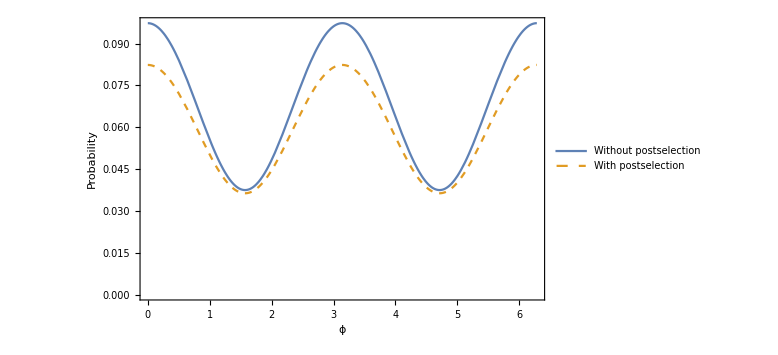

```mathematica
ClearAll[𝓇,ξ]
𝓇=0.5;
ξ=0.5;
Plot[{wopscoin[ϕ,𝓇,ξ],wpscoin[ϕ,𝓇,ξ]},{ϕ,0,2π},FrameLabel-> {"ϕ","Probability","Visibility (w/o , w ) postselection = ("<>ToString[Vwocoin[𝓇,ξ]]<>" , "<>ToString[Vwcoin[𝓇,ξ]]<>")"},Frame-> True,PlotLegends->{"Without postselection","With postselection"},PlotStyle-> {Solid,Dashed},PlotRange->{0,Automatic},Ticks->{{0,π/2,π,(3π)/2,2π},Automatic},ImageSize->Large,LabelStyle->Large]
ClearAll[𝓇,ξ]
```

## Attenuators in the upper arm only (inefficient detectors)

## Setup

#### Beam splitter transformation

```mathematica
B[r_,t_]={{t,-r},{r,t}};
```

```mathematica
(* Creation operators are representated by c *)
```

#### First beam splitter

```mathematica
{ca0,cb0}=B[1/(√2),1/(√2)].{ca1,cb1};
```

#### Phase shift in lower path

```mathematica
cb1=ⅇ^(-ⅈ ϕ)cb2;
```

#### Second and ‘Fourth’ beam splitters

```mathematica
{ca1,cc1}=B[𝓇,𝓉].{ca2p,cc2};
{cb2,cd1}=B[1,0].{cb3p,cd2};
```

#### Fifth and Sixth beam splitters (to simulate inefficient detectors in modes a and b)

```mathematica
{ca2p,cadumpp}=B[𝓇loss,𝓉loss].{ca2,cadump};
{cb3p,cbdumpp}=B[𝓇loss,𝓉loss].{cb3,cbdump};
```

#### Third beam splitter

```mathematica
{cc2,cd2}=B[1/(√2),1/(√2)].{cc3,cd3};
```

```mathematica
𝓇loss=√(0.10/2);(*10% total loss of photons in both detectors, due to inefficiency *)
𝓉loss=√(1-𝓇loss^2);
```

## 1. Single-Mode Squeezed Vacuum

### SMSV in mode a

```mathematica
ClearAll[S,out]
S[ξ_,n_]=1/(√Cosh[ξ])∑_(k=0)^n √Binomial[2k,k](-Tanh[ξ]/2)^k ca0^(2k)/(√((2k)!)); (* Source: Wikipedia*)
(* S[ξ,n] approximates single mode squeezed vacuum up to photon number = 2n *)
out[ca2_,cb3_,n_]=S[ξ,n];
Prob[n_,ξ_]=Sech[ξ]∑_(k=0)^n Binomial[2k,k](Tanh[ξ]/2)^(2k);
```

### Observing interference with and without postselection on modes a and b

#### c=1,d=1

```mathematica
ClearAll[n,a,b,c,d,wopostselect,wpostselect]
n=5;  (* Squeezed states approximated with 2n terms *)
a=0;  (* postselection on mode a *)
b=0;  (* postselection on mode b *)
c=1; (* amplitude for mode c chosen to observe the interference  *)
d=1;(* amplitude for mode d chosen to observe the interference  *)

wopostselect[ϕ_,𝓇_,ξ_] = Module[{ψ,P},
𝓉=√(1-𝓇^2);
ψ =√(c!d!)CoefficientList[CoefficientList[out[ca,cb,n],{cc3,cd3}][[c+1,d+1]],{ca,cb,cadump,cbdump}];
P=Table[Abs[√((i-1)!   (j-1)!(k-1)!(l-1)!)ψ[[i,j,k,l]]]^2,{i,1,Dimensions[ψ][[1]]},{j,1,Dimensions[ψ][[2]]},{k,1,Dimensions[ψ][[3]]},{l,1,Dimensions[ψ][[4]]}];
Total[P,4]/Prob[n,ξ]
];
wpostselect[ϕ_,𝓇_,ξ_]=Module[{ψ,P},
𝓉=√(1-𝓇^2);
ψ=√(c!d! a!b!)CoefficientList[out[ca,cb,n],{cc3,cd3,ca,cb,cadump,cbdump}][[c+1,d+1,a+1,b+1]];
P=Table[Abs[√((k-1)!(l-1)!)ψ[[k,l]]]^2,{k,1,Dimensions[ψ][[1]]},{l,1,Dimensions[ψ][[2]]}];
Total[P,2]/Prob[n,ξ]
];
Vwo[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=FindMaximum[wopostselect [x,𝓇,ξ],{x,3 π/4}][[1]];
Imin = FindMinimum[wopostselect [x,𝓇,ξ],{x,3 π/4}][[1]];
N[(Imax-Imin)/(Imax+ Imin)]
];
Vw[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=FindMaximum[wpostselect[x,𝓇,ξ],{x,3 π/4}][[1]];
Imin = FindMinimum[wpostselect [x,𝓇,ξ],{x,3 π/4}][[1]];
N[(Imax-Imin)/(Imax+ Imin)]
];
```

```mathematica
ClearAll[𝓇,ξ]
Plot[{Vwo[0.9,ξ],Vwo[0.7,ξ],Vwo[0.5,ξ],Vwo[0.3,ξ],Vwo[0.1,ξ]},{ξ,0.01,4},PlotRange->Full,Frame->True,FrameLabel->{"Squeezing Par. ξ","Visibility","Vis. w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,ImageSize->Scaled[0.25]]
Plot[{wopostselect[π/2,0.9,ξ],wopostselect[π/2,0.7,ξ],wopostselect[π/2,0.5,ξ],wopostselect[π/2,0.3,ξ],wopostselect[π/2,0.1,ξ]},{ξ,0.01,4},PlotRange->{0,Full},Frame->True,FrameLabel->{"Squeezing Par. ξ","Probability","Max Prob. of Success w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,ImageSize->Scaled[0.30]]
ClearAll[𝓇,ξ]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum::lstol will be suppressed during this calculation.

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

-Graphics-

-Graphics-

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum::lstol will be suppressed during this calculation.

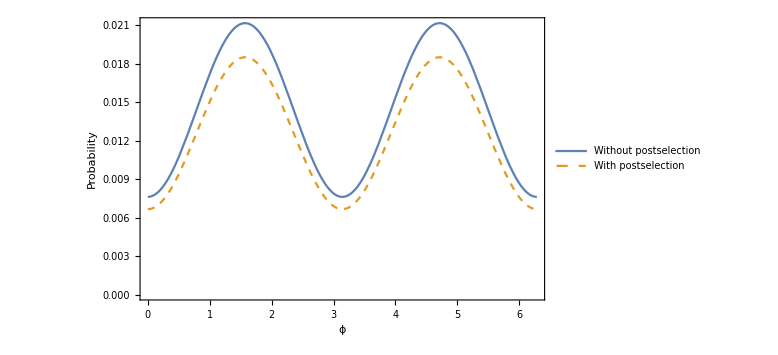

```mathematica
𝓇=0.5;
ξ=0.5;
Plot[{wopostselect[ϕ,𝓇,ξ],wpostselect[ϕ,𝓇,ξ]},{ϕ,0,2π},FrameLabel-> {"ϕ","Probability","Visibility (w/o , w ) postselection = ("<>ToString[Vwo[𝓇,ξ]]<>" , "<>ToString[Vw[𝓇,ξ]]<>") for 𝓇=0.5, ξ=1.462"},Frame-> True,PlotLegends->{"Without postselection","With postselection"},PlotStyle-> {Solid,Dashed},PlotRange->{0,Automatic},Ticks->{{0,π/2,π,(3π)/2,2π},Automatic},ImageSize->Large,LabelStyle->Large]
ClearAll[𝓇,ξ]
```

#### c=2,d=2

```mathematica
ClearAll[n,a,b,c,d,wopostselect,wpostselect]
n=10;  (* Squeezed states approximated with 2n terms *)
a=0;  (* postselection on mode a *)
b=0;  (* postselection on mode b *)
c=2; (* amplitude for mode c chosen to observe the interference  *)
d=2;(* amplitude for mode d chosen to observe the interference  *)
wopostselect[ϕ_,𝓇_,ξ_] = Module[{ψ,P},
𝓉=√(1-𝓇^2);
ψ =√(c!d!)CoefficientList[CoefficientList[out[ca,cb,n],{cc3,cd3}][[c+1,d+1]],{ca,cb,cadump,cbdump}];
P=Table[Abs[√((i-1)!   (j-1)!(k-1)!(l-1)!)ψ[[i,j,k,l]]]^2,{i,1,Dimensions[ψ][[1]]},{j,1,Dimensions[ψ][[2]]},{k,1,Dimensions[ψ][[3]]},{l,1,Dimensions[ψ][[4]]}];
Total[P,4]/Prob[n,ξ]
];
wpostselect[ϕ_,𝓇_,ξ_]=Module[{ψ,P},
𝓉=√(1-𝓇^2);
ψ=√(c!d! a!b!)CoefficientList[out[ca,cb,n],{cc3,cd3,ca,cb,cadump,cbdump}][[c+1,d+1,a+1,b+1]];
P=Table[Abs[√((k-1)!(l-1)!)ψ[[k,l]]]^2,{k,1,Dimensions[ψ][[1]]},{l,1,Dimensions[ψ][[2]]}];
Total[P,2]/Prob[n,ξ]
];
Vwo[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=FindMaximum[wopostselect [x,𝓇,ξ],{x,3 π/4}][[1]];
Imin = FindMinimum[wopostselect [x,𝓇,ξ],{x,3 π/4}][[1]];
N[(Imax-Imin)/(Imax+ Imin)]
];
Vw[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=FindMaximum[wpostselect[x,𝓇,ξ],{x,3 π/4}][[1]];
Imin = FindMinimum[wpostselect [x,𝓇,ξ],{x,3 π/4}][[1]];
N[(Imax-Imin)/(Imax+ Imin)]
];
(*Manipulate[Plot[{wopostselect [ϕ,𝓇,ξ],wpostselect[ϕ,𝓇,ξ]},{ϕ,0,2π},PlotLabel-> "Visibility (w/o , w ) postselection = ("<>ToString[Vwo[𝓇,ξ]]<>" , "<>ToString[Vw[𝓇,ξ]]<>")",AxesLabel-> {ϕ,P},PlotLegends->{"Without postselection","With postselection"},Ticks->{{0,π/2,π,(3π)/2,2π},Automatic},PlotStyle-> {Solid,Dashed},PlotRange->Full,ImageSize->Medium],{ξ,5,10,Appearance-> "Open"},{𝓇,0.1,1,Appearance-> "Open"}]*)
```

{0.0329238,{𝓇→0.548607,ξ→6.44921}}

-Graphics-

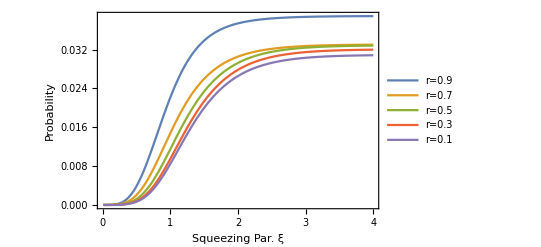

```mathematica
ClearAll[𝓇,ξ]
FindMaximum[{wopostselect[π/2,𝓇,ξ],0≤𝓇≤1&&0<ξ},{𝓇,0.5},{ξ,1}]
Plot[{Vwo[0.9,ξ],Vwo[0.7,ξ],Vwo[0.5,ξ],Vwo[0.3,ξ],Vwo[0.1,ξ]},{ξ,0.01,4},PlotRange->Full,Frame->True,FrameLabel->{"Squeezing Par. ξ","Visibility","Vis. w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,ImageSize->Scaled[0.25]]
Plot[{wopostselect[π/2,0.9,ξ],wopostselect[π/2,0.7,ξ],wopostselect[π/2,0.5,ξ],wopostselect[π/2,0.3,ξ],wopostselect[π/2,0.1,ξ]},{ξ,0.01,4},PlotRange->{0,Full},Frame->True,FrameLabel->{"Squeezing Par. ξ","Probability","Max Prob. of Success w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,ImageSize->Scaled[0.30]]
ClearAll[𝓇,ξ]
```

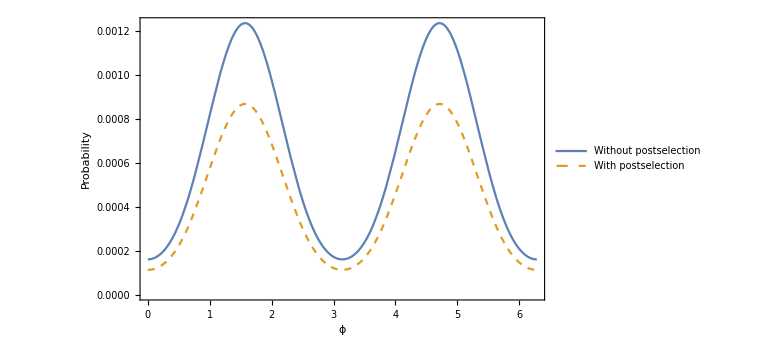

```mathematica
ClearAll[𝓇,ξ]
𝓇=0.5;
ξ=0.5;
Plot[{wopostselect[ϕ,𝓇,ξ],wpostselect[ϕ,𝓇,ξ]},{ϕ,0,2π},FrameLabel-> {"ϕ","Probability","Visibility (w/o , w ) postselection = ("<>ToString[Vwo[𝓇,ξ]]<>" , "<>ToString[Vw[𝓇,ξ]]<>") for 𝓇=0.5, ξ=1.462"},Frame-> True,PlotLegends->{"Without postselection","With postselection"},PlotStyle-> {Solid,Dashed},PlotRange->{0,Automatic},Ticks->{{0,π/2,π,(3π)/2,2π},Automatic},ImageSize->Large,LabelStyle->Large]
ClearAll[𝓇,ξ]
```

## 2. Two-Mode Squeezed Vacuum Input and observing interference for P(1,1)

```mathematica
(* T[ξ_,n_]=1/Cosh[ξ]∑_(k=0)^n (-Tanh[ξ]/1)^k(ca0^k cb0^k)/(k!); (* Source: Wikipedia*)*)
(* T[ξ,n] approximates two mode squeezed vacuum up to photon number = n,n *)
ClearAll[out2,n]
n=5;
out2[ca2_,cb3_]=1/Cosh[ξ] Sum[(-Tanh[ξ]/1 ca0 cb0)^k/k!,{k,0,n}];
Prob[n_,ξ_]=Sech[ξ]^2(1-Tanh[ξ]^(2(n+1)))/(1-Tanh[ξ]^2);
```

```mathematica
(* Approximation of taking only a few terms *)
```

```mathematica
ClearAll[a,b,c,d,wopostselect2,wpostselect2]
a=0;  (* postselection on mode a *)
b=0;  (* postselection on mode b *)
c=1; (* amplitude for mode c chosen to observe the interference  *)
d=1;(* amplitude for mode d chosen to observe the interference  *)

wopostselect2[ϕ_,𝓇_,ξ_] = Module[{ψ,P},
𝓉=√(1-𝓇^2);
ψ =√(c!d!)CoefficientList[out2[ca,cb],{cc3,cd3,ca,cb,cadump,cbdump}][[c+1,d+1]];
P=Table[Abs[√((i-1)!   (j-1)!(k-1)!(l-1)!)ψ[[i,j,k,l]]]^2,{i,1,Dimensions[ψ][[1]]},{j,1,Dimensions[ψ][[2]]},{k,1,Dimensions[ψ][[3]]},{l,1,Dimensions[ψ][[4]]}];
Total[P,4]/Prob[n,ξ]
];
wpostselect2[ϕ_,𝓇_,ξ_]=Module[{ψ,P},
𝓉=√(1-𝓇^2);
ψ=√(c!d! a!b!)CoefficientList[out2[ca,cb],{cc3,cd3,ca,cb,cadump,cbdump}][[c+1,d+1,a+1,b+1]];
P=Table[Abs[√((k-1)!(l-1)!)ψ[[k,l]]]^2,{k,1,Dimensions[ψ][[1]]},{l,1,Dimensions[ψ][[2]]}];
Total[P,2]/Prob[n,ξ]
];

(* Visibility *)
Vwo2[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=wopostselect2 [0,𝓇,ξ];
Imin =wopostselect2 [Pi/2,𝓇,ξ];
N[(Imax-Imin)/(Imax+ Imin)]
];
Vw2[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=wpostselect2 [0,𝓇,ξ];
Imin =wpostselect2 [Pi/2,𝓇,ξ];
N[(Imax-Imin)/(Imax+ Imin)]
];
```

```mathematica
Plot[{Vwo2[0.9,ξ],Vwo2[0.7,ξ],Vwo2[0.5,ξ],Vwo2[0.32,ξ],Vwo2[0.1,ξ]},{ξ,0.01,4},PlotRange->Full,Frame->True,GridLines->{ {},{}},FrameLabel->{"Squeezing Par. ξ","Visibility","Vis. w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,ImageSize->Scaled[0.25]]
Plot[{wopostselect2[0,0.9,ξ],wopostselect2 [0,0.7,ξ],wopostselect2[0,0.5,ξ],wopostselect2[0,0.3,ξ],wopostselect2[0,0.1,ξ]},{ξ,0.01,4},PlotRange->{0,Full},Frame->True,FrameLabel->{"Squeezing Par. ξ","Probability","Max Prob. of Success w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,GridLines-> {{},{}},ImageSize->Scaled[0.30]]
```

-Graphics-

-Graphics-

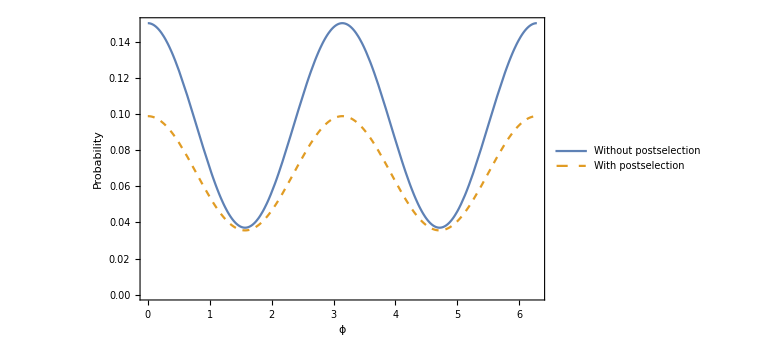

```mathematica
ClearAll[𝓇,ξ]
𝓇=0.5;
ξ=1;
Plot[{wopostselect2[ϕ,𝓇,ξ],wpostselect2[ϕ,𝓇,ξ]},{ϕ,0,2π},FrameLabel-> {"ϕ","Probability","Visibility (w/o , w ) postselection = ("<>ToString[Vwo2[𝓇,ξ]]<>" , "<>ToString[Vw2[𝓇,ξ]]<>")"},Frame-> True,PlotLegends->{"Without postselection","With postselection"},PlotStyle-> {Solid,Dashed},PlotRange->{0,Automatic},Ticks->{{0,π/2,π,(3π)/2,2π},Automatic},ImageSize->Large,LabelStyle->Large]
ClearAll[𝓇,ξ]
```

## 3. Two-Mode Squeezed Vacuum Input and observing interference for P(coincidence w/o PNR) = P(not 0,not 0) = P(any,any)-P(0,any)-P(any,0)+P(0,0)

```mathematica
ClearAll[outcoin,n]
n=5;
outcoin[ca2_,cb3_]=1/Cosh[ξ] Sum[(-Tanh[ξ]/1 ca0 cb0)^k/k!,{k,0,n}];
(* Approximation of taking only a few terms *)
ClearAll[wopscoin,wpscoin,a,b,c,d]
a=0;  (* postselection on mode a *)
b=0;  (* postselection on mode b *)
(*c=1; (* amplitude for mode c chosen to observe the interference  *)
d=1;(* amplitude for mode d chosen to observe the interference  *)*)
Prob[n_,ξ_]=Sech[ξ]^2(1-Tanh[ξ]^(2(n+1)))/(1-Tanh[ξ]^2);
wopscoin[ϕ_,𝓇_,ξ_]=Module[{ψp,ψ,P},
𝓉=√(1-𝓇^2);
ψp=CoefficientList[outcoin[ca,cb],{cc3,cd3,ca,cb,cadump,cbdump}];
ψ =Table[√((i-1)!(j-1)!(k-1)!(l-1)!(g-1)!(h-1)!)ψp[[i,j,k,l,g,h]],{i,1,Dimensions[ψp][[1]]},{j,1,Dimensions[ψp][[2]]},{k,1,Dimensions[ψp][[3]]},{l,1,Dimensions[ψp][[4]]},{g,1,Dimensions[ψp][[5]]},{h,1,Dimensions[ψp][[6]]}];
P=Table[Total[Table[Abs[ψ[[i,j]][[k,l,g,h]]]^2,{k,1,Dimensions[ψ[[i,j]]][[1]]},{l,1,Dimensions[ψ[[i,j]]][[2]]},{g,1,Dimensions[ψ[[i,j]]][[3]]},{h,1,Dimensions[ψ[[i,j]]][[4]]}],4],{i,1,Dimensions[ψ][[1]]},{j,1,Dimensions[ψ][[2]]}];
(Total[P,2]-Total[P,{1}][[1]]-Total[P,{2}][[1]]+P[[1,1]])/Prob[n,ξ]
];
wpscoin[ϕ_,𝓇_,ξ_]=Module[{ψp,ψ,P},
𝓉=√(1-𝓇^2);
ψp=CoefficientList[outcoin[ca,cb],{cc3,cd3,ca,cb,cadump,cbdump}];
ψ =Table[√((i-1)!(j-1)!(k-1)!(l-1)!(g-1)!(h-1)!)ψp[[i,j,k,l,g,h]],{i,1,Dimensions[ψp][[1]]},{j,1,Dimensions[ψp][[2]]},{k,1,Dimensions[ψp][[3]]},{l,1,Dimensions[ψp][[4]]},{g,1,Dimensions[ψp][[5]]},{h,1,Dimensions[ψp][[6]]}];
P=Table[Total[Table[Abs[ψ[[i,j]][[a+1,b+1,g,h]]]^2,{g,1,Dimensions[ψ[[i,j]][[a+1,b+1]]][[1]]},{h,1,Dimensions[ψ[[i,j]][[a+1,b+1]]][[2]]}],2],{i,1,Dimensions[ψ][[1]]},{j,1,Dimensions[ψ][[2]]}];
(Total[P,2]-Total[P,{1}][[1]]-Total[P,{2}][[1]]+P[[1,1]])/Prob[n,ξ]
];
(* Visibility *)
Vwocoin[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=wopscoin [0,𝓇,ξ];
Imin =wopscoin [Pi/2,𝓇,ξ];
N[(Imax-Imin)/(Imax+ Imin)]
];
Vwcoin[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=wpscoin [0,𝓇,ξ];
Imin =wpscoin [Pi/2,𝓇,ξ];
N[(Imax-Imin)/(Imax+ Imin)]
];
```

```mathematica
Plot[{Vwocoin[0.9,ξ],Vwocoin[0.7,ξ],Vwocoin[0.5,ξ],Vwocoin[0.3,ξ],Vwocoin[0.1,ξ]},{ξ,0.01,4},PlotRange->Full,GridLines->{{},{}},Frame->True,FrameLabel->{"Squeezing Par. ξ","Visibility","Vis. w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,ImageSize->Scaled[0.25]]
Plot[{wopscoin[0,0.9,ξ],wopscoin [0,0.7,ξ],wopscoin[0,0.5,ξ],wopscoin[0,0.3,ξ],wopscoin[0,0.1,ξ]},{ξ,0.01,4},PlotRange->{0,Full},Frame->True,FrameLabel->{"Squeezing Par. ξ","Probability","Max Prob. of Success w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},GridLines->{{},{}},LabelStyle->Large,ImageSize->Scaled[0.30]]
```

-Graphics-

-Graphics-

```mathematica
ClearAll[𝓇,ξ]
𝓇=0.5;
ξ=0.5;
Plot[{wopscoin[ϕ,𝓇,ξ],wpscoin[ϕ,𝓇,ξ]},{ϕ,0,2π},FrameLabel-> {"ϕ","Probability","Visibility (w/o , w ) postselection = ("<>ToString[Vwocoin[𝓇,ξ]]<>" , "<>ToString[Vwcoin[𝓇,ξ]]<>")"},Frame-> True,PlotLegends->{"Without postselection","With postselection"},PlotStyle-> {Solid,Dashed},PlotRange->{0,Automatic},Ticks->{{0,π/2,π,(3π)/2,2π},Automatic},ImageSize->Large,LabelStyle->Large]
ClearAll[𝓇,ξ]
```

-Graphics-

## SMSV Wigner function

## Wigner function

Convention: α =  (a+ⅈ b)/(√2) ⇒ a = √2 Re[ α]

### Number State

```mathematica
Wn[a_,b_,n_]:= 1/π(-1)^n LaguerreL[n,2(a^2+b^2)] ⅇ^(-(a^2+b^2));
```

### SMSV Exact

```mathematica
Wsqueezed[x_,p_,s_]:=1/π ⅇ^(-s x^2- p^2/s);
Plot3D[Wsqueezed[x,p,3],{x,-3.5,3.5},{p,-3.5,3.5},PlotRange->Full,PlotPoints->25,Mesh->Automatic, ColorFunction->"Rainbow",PlotStyle->Opacity[0.8],AxesLabel->Automatic,LabelStyle->Large]
```

### SMSV Approx. using few number states

#### Check: Assuming that the Wigner function is a linear transformation (It is not)

```mathematica
Wsqa[a_,b_,ξ_,n_]:=1/(√Cosh[ξ])∑_(k=0)^n √Binomial[2k,k] Wn[a,b,2k](-Tanh[ξ]/2)^k;
Plot3D[Wsqa[x,p,3,10],{x,-3.5,3.5},{p,-3.5,3.5},PlotRange->Full,PlotPoints->25,Mesh->Automatic, ColorFunction->"Rainbow",PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->Automatic,LabelStyle->Large]
```

This shows that Wigner function is not a linear transformation.

### Calculation of the Wigner function from the pure squeezed state wave function

```mathematica
ψsq[s_,x_]:=(s/π)^(1/4)ⅇ^(-s/2 x^2);
Wsqcal[s_,x_,p_]:=1/(2π)NIntegrate[ⅇ^(ⅈ p y)Conjugate[(ψsq[s,x-1/2 y])] ψsq[s,x+1/2 y],{y,-100,100}];
(*Plot3D[Wsqcal[0.5,a,b],{a,-3.5,3.5},{b,-3.5,3.5},PlotRange->Full,PlotPoints->25,Mesh->Automatic, ColorFunction->"Rainbow",PlotStyle->Opacity[0.8],PlotRange->Full]*)
```

```mathematica
ClearAll[limits,range,s]
limits=3.5;
range=10;
s=3;
matWsqcal=Table[Re[Chop[Wsqcal[s,(x-1)limits/range-limits,(p-1)limits/range-limits]]],{p,1,2 range +1},{x,1,2 range +1}];

ListPlot3D[matWsqcal,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->Automatic, ColorFunction->"Rainbow",PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p},LabelStyle->Large]
ClearAll[limits,range,s]
```

### Calculation of the Wigner function using number states (and approx. by taking few terms)

```mathematica
ψn[n_,x_]=(ⅇ^(-x^2/2))/(π^(1/4)√(n!2^n))HermiteH[n,x];
ψsqapprox[ξ_,nlim_,x_]=1/(√Cosh[ξ])∑_(k=0)^nlim √Binomial[2k,k](-Tanh[ξ]/2)^k ψn[2k,x];
nlim=5;
Wsqapprox[ξ_,nlim_,x_,p_]:=1/(2π)NIntegrate[ⅇ^(ⅈ p y)Conjugate[(ψsqapprox[ξ,nlim,x-1/2 y])] ψsqapprox[ξ,nlim,x+1/2 y],{y,-50,50}];
ClearAll[limits,range,ξ,s]
limits=3.5;
range=10;
s=3;
ξ=1/2 Log[s];
matWsqapprox=Table[Re[Chop[Wsqapprox[ξ,nlim,(x-1)limits/range-limits,(p-1)limits/range-limits]]],{p,1,2 range +1},{x,1,2 range +1}];

ListPlot3D[matWsqapprox,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->Automatic,ColorFunction->"Rainbow",PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p},LabelStyle->Large]
ClearAll[limits,range,ξ,s]
```

## SMSV → NA → Homodyne

## Setup

#### Beam splitter transformation

```mathematica
B[r_,t_]={{t,-r},{r,t}};
```

```mathematica
(* Creation operators are representated by c *)
```

#### NA

```mathematica
{ca0,cb0}=B[𝓇,𝓉].{ca,cb};
```

### Input State: SMSV

```mathematica
S[ξ_,n_]=1/(√Cosh[ξ])∑_(k=0)^n √Binomial[2k,k](-Tanh[ξ]/2)^k ca0^(2k)/(√((2k)!));
```

```mathematica
b=0;(* Post selection *)
coeff[ξ_,nlim_]:=CoefficientList[S[ξ,nlim],{cb,ca}];
ψout[ξ_,nlim_,x_]:=Total[Table[√(b!(i-1)!)coeff[ξ,nlim][[b+1,i]]ψn[i-1,x],{i,1,Dimensions[coeff[ξ,nlim]][[2]]}]];
```

```mathematica
ClearAll[𝓇,𝓉]
𝓇=0.5;
𝓉=√(1-𝓇^2);
nlim=5;
W[ξ_,nlim_,x_,p_]:=1/(2π)NIntegrate[ⅇ^(ⅈ p y)Conjugate[(ψout[ξ,nlim,x-1/2 y])] ψout[ξ,nlim,x+1/2 y],{y,-50,50}];
ClearAll[limits,range,ξ,s]
limits=3.5;
range=10;
s=3;
ξ=1/2 Log[s];
wpsmat=Table[Re[Chop[W[ξ,nlim,(x-1)limits/range-limits,(p-1)limits/range-limits]]],{p,1,2 range +1},{x,1,2 range +1}];

ListPlot3D[wpsmat,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->Automatic,ColorFunction->"Rainbow",PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p},LabelStyle->Large]
ClearAll[limits,range,ξ,s]
ClearAll[𝓇,𝓉]
```

-Graphics3D-

## Is the attenuation noiseless? SMSV → Attenuation (w/o post selection) →Homodyne

## Setup

#### Beam splitter transformation

```mathematica
B[r_,t_]={{t,-r},{r,t}};
```

```mathematica
(* Creation operators are representated by c *)
```

#### NA

```mathematica
{ca0,cb0}=B[𝓇,𝓉].{ca,cb};
```

### Input State: SMSV

```mathematica
S[ξ_,n_]=1/(√Cosh[ξ])∑_(k=0)^n √Binomial[2k,k](-Tanh[ξ]/2)^k ca0^(2k)/(√((2k)!));
```

```mathematica
b=0;(* Post selection *)
coeff[ξ_,nlim_]:=CoefficientList[S[ξ,nlim],{cb,ca}];
ψout[ξ_,nlim_,x_]:=Module[{coefftable},
coefftable=coeff[ξ,nlim];
Table[Total[Table[√((i-1)!(j-1)!)coefftable[[i,j]]ψn[j-1,x],{j,1,Dimensions[coefftable][[2]]}]],{i,1,Dimensions[coefftable][[1]]}]
];
```

```mathematica
ClearAll[𝓇,𝓉]
𝓇=0.5;
𝓉=√(1-𝓇^2);
nlim=5;
wopsW[ξ_,nlim_,x_,p_]:=Module[{coefftable,dim,Pr},
coefftable=coeff[ξ,nlim];
dim=Dimensions[coefftable];
Pr=Table[Abs[√((i-1)!(j-1)!)coefftable[[i,j]]]^2,{i,1,dim[[1]]},{j,1,dim[[2]]}];
Total[Table[(Total[Pr,{2}][[i]])/(2π)NIntegrate[ⅇ^(ⅈ p y)Conjugate[(ψout[ξ,nlim,x-1/2 y][[i]])] ψout[ξ,nlim,x+1/2 y][[i]],{y,-50,50}],{i,1,dim[[1]]}]]
];
ClearAll[limits,range,ξ,s]
limits=3.5;
range=10;
s=3;
ξ=1/2 Log[s];
wopsmat=Table[Re[Chop[wopsW[ξ,nlim,(x-1)limits/range-limits,(p-1)limits/range-limits]]],{p,1,2 range +1},{x,1,2 range +1}];

ListPlot3D[wopsmat,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->Automatic,ColorFunction->"Rainbow",PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p},LabelStyle->Large]
ClearAll[limits,range,ξ,s]
ClearAll[𝓇,𝓉]
```

## Model fitting

### Before

```mathematica
model=a Exp[(-(s x^2+p^2/s))/(2 σ^2)];
range =(Dimensions[matWsqapprox][[1]]-1)/2;
```

```mathematica
IdxData= Table[{i-range -1,j-range-1,matWsqapprox[[i,j]]},{i,1,2range+1},{j,1,2range+1}];
Data=Flatten[IdxData,1];
fit = FindFit[Data,model,{{a,0.5},σ,s},{p,x}]
```

{a→0.318252,σ→2.02043,s→2.9934}

### After (attenuation w/ post selection)

```mathematica
model=a Exp[(-(s x^2+p^2/s))/(2 σ^2)];
range =(Dimensions[wpsmat][[1]]-1)/2;
IdxData= Table[{i-range -1,j-range-1,wpsmat[[i,j]]},{i,1,2range+1},{j,1,2range+1}];
Data=Flatten[IdxData,1];
fit = FindFit[Data,model,{{a,0.5},σ,s},{p,x}]
```

{a→0.297363,σ→2.02031,s→2.19978}

### After (attenuation w/o post selection)

```mathematica
model=a Exp[(-(s x^2+p^2/s))/(2 σ^2)];
range =(Dimensions[wopsmat][[1]]-1)/2;
IdxData= Table[{i-range -1,j-range-1,wopsmat[[i,j]]},{i,1,2range+1},{j,1,2range+1}];
Data=Flatten[IdxData,1];
fit = FindFit[Data,model,{{a,0.5},σ,s},{p,x}]
```

{a→0.277011,σ→2.02633,s→2.20025}

## Cat States through noiseless attenuation

### Backup

```mathematica
matCatExact2038={{0.000021804912099780283,0.00001747208237869526,0.000012232872567939392,3.6609957824521978*^-6,-0.000019867543527424462,-0.00005215641837784108,-0.00011660857109764363,-0.00017832214213447015,-0.00020057672257507331,-0.00017832214213446792,-0.00011660857109764032,-0.000052156418377842184,-0.000019867543527425983,3.6609957824504724*^-6,0.000012232872567940048,0.000017472082378703534,0.00002180491209977959},{0.00015948950732782294,0.0001543096460895404,0.00011515301891291918,0.00006219544237978975,0.0000136732200790979,-0.000028382396320037478,-0.00006791679196582772,-0.00010303751860059644,-0.00012735956070186714,-0.0001030375186005909,-0.00006791679196582441,-0.00002838239632003803,0.000013673220079097623,0.00006219544237978941,0.00011515301891292196,0.00015430964608955004,0.0001594895073278243},{0.0009790413424703723,0.0009681368353103532,0.0007331590191950649,0.00046621917018342635,0.00039173949737305116,0.000640661003142181,0.0011892175252545332,0.0017957695243085757,0.0020685120253841668,0.0017957695243085762,0.0011892175252545332,0.0006406610031421844,0.00039173949737305165,0.0004662191701834257,0.0007331590191950606,0.0009681368353103538,0.000979041342470373},{0.004592173318530384,0.0045347876877358554,0.003361973813196784,0.001793422939167781,0.00040552444440876845,-0.0008202755677980638,-0.0021132406848250436,-0.0033082596542262344,-0.003819100744458539,-0.00330825965422623,-0.002113240684825046,-0.0008202755677980646,0.00040552444440876813,0.0017934229391677813,0.0033619738131967824,0.004534787687735855,0.004592173318530382},{0.01628005956395258,0.016068913720617712,0.011875445488676487,0.006175208275190183,0.0008170648474899579,-0.004578455046158428,-0.01089007157502701,-0.01690324729452063,-0.019491404086889444,-0.016903247294520626,-0.010890071575027008,-0.004578455046158431,0.0008170648474899568,0.006175208275190183,0.011875445488676487,0.016068913720617712,0.016280059563952582},{0.0435861278702056,0.04314924326205106,0.032682783790316305,0.020737345021525834,0.01709250130556963,0.02764246742260182,0.05145873767453376,0.07766524215762378,0.08929460760780802,0.07766524215762378,0.05145873767453376,0.02764246742260182,0.01709250130556963,0.020737345021525834,0.032682783790316305,0.04314924326205107,0.0435861278702056},{0.08801317480361508,0.0868936807748149,0.0643530226762351,0.034082870995496124,0.006870160987750096,-0.018174693323193884,-0.04556827843306632,-0.0710990806163026,-0.08203097593990248,-0.07109908061630259,-0.04556827843306632,-0.018174693323193884,0.006870160987750097,0.034082870995496124,0.0643530226762351,0.0868936807748149,0.08801317480361509},{0.1342026571479721,0.13248079739357788,0.09801162281529548,0.05140568623771104,0.008453204543911654,-0.03313160629090622,-0.08042687072013033,-0.125099154456458,-0.14428784420140606,-0.125099154456458,-0.08042687072013036,-0.033131606290906224,0.008453204543911654,0.05140568623771104,0.09801162281529548,0.13248079739357788,0.13420265714797208},{0.154525083156304,0.1529738143277202,0.11586868671160355,0.0735517470374592,0.06074510630187821,0.09839767372774391,0.18323048043180892,0.27655721471402006,0.31797041094966283,0.27655721471402006,0.18323048043180895,0.09839767372774391,0.06074510630187821,0.07355174703745922,0.11586868671160354,0.15297381432772017,0.154525083156304},{0.1342026571479721,0.13248079739357788,0.09801162281529548,0.05140568623771104,0.008453204543911654,-0.03313160629090622,-0.08042687072013033,-0.125099154456458,-0.14428784420140606,-0.125099154456458,-0.08042687072013036,-0.033131606290906224,0.008453204543911654,0.05140568623771104,0.09801162281529548,0.13248079739357788,0.13420265714797208},{0.08801317480361508,0.0868936807748149,0.0643530226762351,0.034082870995496124,0.006870160987750096,-0.018174693323193884,-0.04556827843306632,-0.0710990806163026,-0.08203097593990248,-0.07109908061630259,-0.04556827843306632,-0.018174693323193884,0.006870160987750097,0.034082870995496124,0.0643530226762351,0.0868936807748149,0.08801317480361509},{0.0435861278702056,0.04314924326205106,0.032682783790316305,0.020737345021525834,0.01709250130556963,0.02764246742260182,0.05145873767453376,0.07766524215762378,0.08929460760780802,0.07766524215762378,0.05145873767453376,0.02764246742260182,0.01709250130556963,0.020737345021525834,0.032682783790316305,0.04314924326205107,0.0435861278702056},{0.01628005956395258,0.016068913720617712,0.011875445488676487,0.006175208275190183,0.0008170648474899579,-0.004578455046158428,-0.01089007157502701,-0.01690324729452063,-0.019491404086889444,-0.016903247294520626,-0.010890071575027008,-0.004578455046158431,0.0008170648474899568,0.006175208275190183,0.011875445488676487,0.016068913720617712,0.016280059563952582},{0.004592173318530384,0.0045347876877358554,0.003361973813196784,0.001793422939167781,0.00040552444440876845,-0.0008202755677980638,-0.0021132406848250436,-0.0033082596542262344,-0.003819100744458539,-0.00330825965422623,-0.002113240684825046,-0.0008202755677980646,0.00040552444440876813,0.0017934229391677813,0.0033619738131967824,0.004534787687735855,0.004592173318530382},{0.0009790413424703723,0.0009681368353103532,0.0007331590191950649,0.00046621917018342635,0.00039173949737305116,0.000640661003142181,0.0011892175252545332,0.0017957695243085757,0.0020685120253841668,0.0017957695243085762,0.0011892175252545332,0.0006406610031421844,0.00039173949737305165,0.0004662191701834257,0.0007331590191950606,0.0009681368353103538,0.000979041342470373},{0.00015948950732782294,0.0001543096460895404,0.00011515301891291918,0.00006219544237978975,0.0000136732200790979,-0.000028382396320037478,-0.00006791679196582772,-0.00010303751860059644,-0.00012735956070186714,-0.0001030375186005909,-0.00006791679196582441,-0.00002838239632003803,0.000013673220079097623,0.00006219544237978941,0.00011515301891292196,0.00015430964608955004,0.0001594895073278243},{0.000021804912099780283,0.00001747208237869526,0.000012232872567939392,3.6609957824521978*^-6,-0.000019867543527424462,-0.00005215641837784108,-0.00011660857109764363,-0.00017832214213447015,-0.00020057672257507331,-0.00017832214213446792,-0.00011660857109764032,-0.000052156418377842184,-0.000019867543527425983,3.6609957824504724*^-6,0.000012232872567940048,0.000017472082378703534,0.00002180491209977959}};
```

```mathematica
wpsmat2038={{0.000014655817738786015,0.000018873375264725016,0.00001845513386333103,0.000012759942805282855,2.562960374525798*^-6,-0.000010257589782431718,-0.000027014638640031845,-0.000042721025495682795,-0.00004903181736799969,-0.000042721025495680924,-0.000027014638640032218,-0.000010257589782429471,2.56296037452299*^-6,0.000012759942805290343,0.000018455133863344697,0.000018873375264723705,0.00001465581773878845},{0.00011948577667145856,0.00015690132252184377,0.00015718954596317616,0.00012575566856577492,0.00009926366072102293,0.00011813986593149335,0.0001914788966444056,0.00028076793207808487,0.0003208385828093401,0.00028076793207808845,0.00019147889664440792,0.00011813986593149303,0.00009926366072102207,0.00012575566856577408,0.0001571895459631772,0.0001569013225218383,0.0001194857766714573},{0.0007422362604714934,0.0009745314090258275,0.000966056179320004,0.0007243808222621376,0.0004152887165193978,0.0001935439391375725,0.0000951943136531066,0.00007383940920272597,0.00007405466558210368,0.0000738394092027274,0.0000951943136531128,0.00019354393913757485,0.0004152887165193993,0.000724380822262138,0.000966056179320007,0.000974531409025832,0.0007422362604714909},{0.003484679546423901,0.004567364790939593,0.00447754074732256,0.003119479806283231,0.000945425988218948,-0.0017805434627075122,-0.004983303243313592,-0.00793426439577006,-0.009184199129023535,-0.00793426439577006,-0.004983303243313593,-0.0017805434627075098,0.0009454259882189494,0.003119479806283234,0.0044775407473225575,0.004567364790939596,0.003484679546423901},{0.01236044152896677,0.016242203683050464,0.016183167515354972,0.01251247620664417,0.008505616446936126,0.007478862562581479,0.010190718548333413,0.014349629417724226,0.01633226000146364,0.014349629417724226,0.01019071854833341,0.007478862562581479,0.008505616446936122,0.01251247620664417,0.016183167515354976,0.016242203683050457,0.012360441528966771},{0.033080906413128205,0.04348768730857512,0.043439891083459324,0.03410011058310277,0.024940541181271914,0.02584452053029561,0.039049401388799136,0.0563601356113287,0.06437752804422632,0.05636013561132868,0.039049401388799136,0.02584452053029559,0.024940541181271907,0.03410011058310277,0.043439891083459324,0.04348768730857512,0.0330809064131282},{0.06678993558029353,0.08755682461832104,0.08594350950130922,0.06039722495739609,0.020294247818379848,-0.028309770622840725,-0.0837673959224917,-0.13416001179423104,-0.1554122731252304,-0.13416001179423095,-0.08376739592249173,-0.02830977062284071,0.020294247818379855,0.06039722495739609,0.0859435095013092,0.08755682461832104,0.06678993558029353},{0.10186298215611019,0.13367649211364901,0.13209372602103195,0.09700321705164937,0.04834557415111984,0.003398789134410865,-0.03366393299642447,-0.061135899963441875,-0.07188425675127033,-0.061135899963441875,-0.03366393299642448,0.0033987891344108663,0.04834557415111985,0.09700321705164935,0.13209372602103195,0.13367649211364901,0.10186298215611019},{0.11729294087433363,0.15426831811799033,0.15457668120173756,0.12357101800862394,0.09791028664974928,0.1170189785746697,0.1897354070635992,0.2780269568898141,0.31826069897188874,0.27802695688981416,0.18973540706359918,0.1170189785746697,0.09791028664974927,0.12357101800862394,0.1545766812017376,0.1542683181179903,0.11729294087433359},{0.10186298215611019,0.13367649211364901,0.13209372602103195,0.09700321705164937,0.04834557415111984,0.003398789134410865,-0.03366393299642447,-0.061135899963441875,-0.07188425675127033,-0.061135899963441875,-0.03366393299642448,0.0033987891344108663,0.04834557415111985,0.09700321705164935,0.13209372602103195,0.13367649211364901,0.10186298215611019},{0.06678993558029353,0.08755682461832104,0.08594350950130922,0.06039722495739609,0.020294247818379848,-0.028309770622840725,-0.0837673959224917,-0.13416001179423104,-0.1554122731252304,-0.13416001179423095,-0.08376739592249173,-0.02830977062284071,0.020294247818379855,0.06039722495739609,0.0859435095013092,0.08755682461832104,0.06678993558029353},{0.033080906413128205,0.04348768730857512,0.043439891083459324,0.03410011058310277,0.024940541181271914,0.02584452053029561,0.039049401388799136,0.0563601356113287,0.06437752804422632,0.05636013561132868,0.039049401388799136,0.02584452053029559,0.024940541181271907,0.03410011058310277,0.043439891083459324,0.04348768730857512,0.0330809064131282},{0.01236044152896677,0.016242203683050464,0.016183167515354972,0.01251247620664417,0.008505616446936126,0.007478862562581479,0.010190718548333413,0.014349629417724226,0.01633226000146364,0.014349629417724226,0.01019071854833341,0.007478862562581479,0.008505616446936122,0.01251247620664417,0.016183167515354976,0.016242203683050457,0.012360441528966771},{0.003484679546423901,0.004567364790939593,0.00447754074732256,0.003119479806283231,0.000945425988218948,-0.0017805434627075122,-0.004983303243313592,-0.00793426439577006,-0.009184199129023535,-0.00793426439577006,-0.004983303243313593,-0.0017805434627075098,0.0009454259882189494,0.003119479806283234,0.0044775407473225575,0.004567364790939596,0.003484679546423901},{0.0007422362604714934,0.0009745314090258275,0.000966056179320004,0.0007243808222621376,0.0004152887165193978,0.0001935439391375725,0.0000951943136531066,0.00007383940920272597,0.00007405466558210368,0.0000738394092027274,0.0000951943136531128,0.00019354393913757485,0.0004152887165193993,0.000724380822262138,0.000966056179320007,0.000974531409025832,0.0007422362604714909},{0.00011948577667145856,0.00015690132252184377,0.00015718954596317616,0.00012575566856577492,0.00009926366072102293,0.00011813986593149335,0.0001914788966444056,0.00028076793207808487,0.0003208385828093401,0.00028076793207808845,0.00019147889664440792,0.00011813986593149303,0.00009926366072102207,0.00012575566856577408,0.0001571895459631772,0.0001569013225218383,0.0001194857766714573},{0.000014655817738786015,0.000018873375264725016,0.00001845513386333103,0.000012759942805282855,2.562960374525798*^-6,-0.000010257589782431718,-0.000027014638640031845,-0.000042721025495682795,-0.00004903181736799969,-0.000042721025495680924,-0.000027014638640032218,-0.000010257589782429471,2.56296037452299*^-6,0.000012759942805290343,0.000018455133863344697,0.000018873375264723705,0.00001465581773878845}};
```

```mathematica
wopsmat2038={{4.493094996364503*^-6,5.959115206987774*^-6,5.730528796538437*^-6,4.340702168019374*^-6,2.3190564816375345*^-6,5.800519145765847*^-7,-5.158817871203533*^-7,-1.2750858333320613*^-6,-1.4717649805167058*^-6,-1.2750858333322678*^-6,-5.158817871205053*^-7,5.800519145769157*^-7,2.3190564816372355*^-6,4.340702168019563*^-6,5.730528796538566*^-6,5.959115206987774*^-6,4.493094996364344*^-6},{0.000036870611114735636,0.000048547762895333604,0.00004801630462431903,0.00003623457212352673,0.000021313814603288626,0.00001147580460928459,8.484649188199265*^-6,9.319680402973274*^-6,0.000010266661490840915,9.319680402973375*^-6,8.484649188198126*^-6,0.000011475804609284552,0.00002131381460328823,0.000036234572123526755,0.00004801630462431947,0.00004854776289533399,0.00003687061111473549},{0.00022951275999262436,0.00030149549826300945,0.00029873501701909165,0.00022356458845768426,0.00012642245955871053,0.00005438068448531046,0.000018540308540812137,6.195300687566876*^-6,3.6675554221089955*^-6,6.195300687567285*^-6,0.00001854030854081214,0.000054380684485310016,0.0001264224595587103,0.00022356458845768388,0.0002987350170190918,0.00030149549826300923,0.0002295127599926242},{0.001078257523786822,0.0014155040924532561,0.001401293915507021,0.001041107207248839,0.0005624945406892519,0.0001717830506259072,-0.00008205031723820328,-0.00022888513462657588,-0.00027950198446388675,-0.0002288851346265742,-0.00008205031723820363,0.00017178305062590712,0.000562494540689251,0.0010411072072488389,0.001401293915507021,0.0014155040924532561,0.001078257523786822},{0.0038231391080388154,0.005019915236560486,0.004977683778275434,0.0037363698892142684,0.0021546922517028918,0.0010384327409108433,0.0005767058698523984,0.0005114183906322236,0.0005316979703096734,0.0005114183906322223,0.000576705869852399,0.0010384327409108433,0.0021546922517028913,0.003736369889214268,0.004977683778275433,0.005019915236560486,0.003823139108038816},{0.010231318580245074,0.013434652518857951,0.013325010398134947,0.010018137661778491,0.005834113505864009,0.002960584715929676,0.0019101086946392016,0.0019278915247016588,0.0020666098541578188,0.0019278915247016605,0.0019101086946392016,0.002960584715929676,0.005834113505864009,0.010018137661778491,0.013325010398134947,0.013434652518857951,0.010231318580245077},{0.020666716771989096,0.02712971232185749,0.026861023402906758,0.019972941346045586,0.010848258104981938,0.0034730627076514013,-0.0012067042929762523,-0.0038291076004869132,-0.004715092614033635,-0.0038291076004869132,-0.0012067042929762523,0.0034730627076514013,0.010848258104981938,0.019972941346045582,0.026861023402906758,0.02712971232185749,0.020666716771989092},{0.03151361845269255,0.04137308801267765,0.04099068481794928,0.030607918401093875,0.017083498785879118,0.006745955962142742,0.0010894074875795147,-0.001371874560928124,-0.00204838252479035,-0.001371874560928124,0.0010894074875795147,0.006745955962142743,0.017083498785879118,0.030607918401093875,0.04099068481794928,0.04137308801267765,0.03151361845269255},{0.03627349422172739,0.04763284876150307,0.04725905745076869,0.03560077705266066,0.02097921285969524,0.011286927241355561,0.008369304053793809,0.009270680349494955,0.010130253065347107,0.009270680349494962,0.008369304053793814,0.011286927241355557,0.020979212859695236,0.03560077705266067,0.04725905745076869,0.04763284876150307,0.03627349422172739},{0.03151361845269255,0.04137308801267765,0.04099068481794928,0.030607918401093875,0.017083498785879118,0.006745955962142742,0.0010894074875795147,-0.001371874560928124,-0.00204838252479035,-0.001371874560928124,0.0010894074875795147,0.006745955962142743,0.017083498785879118,0.030607918401093875,0.04099068481794928,0.04137308801267765,0.03151361845269255},{0.020666716771989096,0.02712971232185749,0.026861023402906758,0.019972941346045586,0.010848258104981938,0.0034730627076514013,-0.0012067042929762523,-0.0038291076004869132,-0.004715092614033635,-0.0038291076004869132,-0.0012067042929762523,0.0034730627076514013,0.010848258104981938,0.019972941346045582,0.026861023402906758,0.02712971232185749,0.020666716771989092},{0.010231318580245074,0.013434652518857951,0.013325010398134947,0.010018137661778491,0.005834113505864009,0.002960584715929676,0.0019101086946392016,0.0019278915247016588,0.0020666098541578188,0.0019278915247016605,0.0019101086946392016,0.002960584715929676,0.005834113505864009,0.010018137661778491,0.013325010398134947,0.013434652518857951,0.010231318580245077},{0.0038231391080388154,0.005019915236560486,0.004977683778275434,0.0037363698892142684,0.0021546922517028918,0.0010384327409108433,0.0005767058698523984,0.0005114183906322236,0.0005316979703096734,0.0005114183906322223,0.000576705869852399,0.0010384327409108433,0.0021546922517028913,0.003736369889214268,0.004977683778275433,0.005019915236560486,0.003823139108038816},{0.001078257523786822,0.0014155040924532561,0.001401293915507021,0.001041107207248839,0.0005624945406892519,0.0001717830506259072,-0.00008205031723820328,-0.00022888513462657588,-0.00027950198446388675,-0.0002288851346265742,-0.00008205031723820363,0.00017178305062590712,0.000562494540689251,0.0010411072072488389,0.001401293915507021,0.0014155040924532561,0.001078257523786822},{0.00022951275999262436,0.00030149549826300945,0.00029873501701909165,0.00022356458845768426,0.00012642245955871053,0.00005438068448531046,0.000018540308540812137,6.195300687566876*^-6,3.6675554221089955*^-6,6.195300687567285*^-6,0.00001854030854081214,0.000054380684485310016,0.0001264224595587103,0.00022356458845768388,0.0002987350170190918,0.00030149549826300923,0.0002295127599926242},{0.000036870611114735636,0.000048547762895333604,0.00004801630462431903,0.00003623457212352673,0.000021313814603288626,0.00001147580460928459,8.484649188199265*^-6,9.319680402973274*^-6,0.000010266661490840915,9.319680402973375*^-6,8.484649188198126*^-6,0.000011475804609284552,0.00002131381460328823,0.000036234572123526755,0.00004801630462431947,0.00004854776289533399,0.00003687061111473549},{4.493094996364503*^-6,5.959115206987774*^-6,5.730528796538437*^-6,4.340702168019374*^-6,2.3190564816375345*^-6,5.800519145765847*^-7,-5.158817871203533*^-7,-1.2750858333320613*^-6,-1.4717649805167058*^-6,-1.2750858333322678*^-6,-5.158817871205053*^-7,5.800519145769157*^-7,2.3190564816372355*^-6,4.340702168019563*^-6,5.730528796538566*^-6,5.959115206987774*^-6,4.493094996364344*^-6}};
```

### Calculation of the Wigner function using number states (and approx. by taking few terms)

```mathematica
ψn[n_,x_]=(ⅇ^(-x^2/2)/(π^(1/4)√(n!2^n)))HermiteH[n,x];
ψc[α_,nlim_,x_]=ⅇ^((-Abs[α]^2)/2)∑_(n=0)^nlim (α^n (ⅇ^(-x^2/2)/(π^(1/4)√(n!2^n)))HermiteH[n,x] )/(√n!);
ψcExact[α_,nlim_,x_]=(1/π^(1/4))ⅇ^((-(x-√2 α)^2)/2);(*checked*)
ψCat[α_,nlim_,x_]=(ψc[α,nlim,x]+ψc[-α,nlim,x])/(√(2(1+ⅇ^(-2 Abs[α]^2))));
nlim=20;
WCat[α_,nlim_,x_,p_]:=(1/(2π))NIntegrate[ⅇ^(-ⅈ p y)Conjugate[(ψCat[α,nlim,x-y/2])] ψCat[α,nlim,x+y/2],{y,-10,10}];
WCatExact[α_,nlim_,x_,p_]:=(ⅇ^(-(x-√2 α)^2-p^2)+ⅇ^(-(x+√2 α)^2-p^2)+2 ⅇ^(-x^2-p^2)Cos[2 √2 α p])/(2π(1+ⅇ^(-2 Abs[α]^2)));(* Typo in https://arxiv.org/pdf/2006.16985.pdf Eq. (27) *)

limits=5;
range=10;
α=2;
matCatExact2=Table[Re[Chop[WCatExact[α,nlim,(x-1)(limits/range)-limits,(p-1)(limits/range)-limits]]],{p,1,2 range +1},{x,1,2 range +1}];
```

```mathematica
matCat=Table[Re[Chop[WCat[α,nlim,(x-1)(limits/range)-limits,(p-1)(limits/range)-limits]]],{p,1,2 range +1},{x,1,2 range +1}];
```

$Aborted

```mathematica
NIntegrate[WCatExact[2,0,x,p],{x,-5,5},{p,-5,5}]
```

0.998934

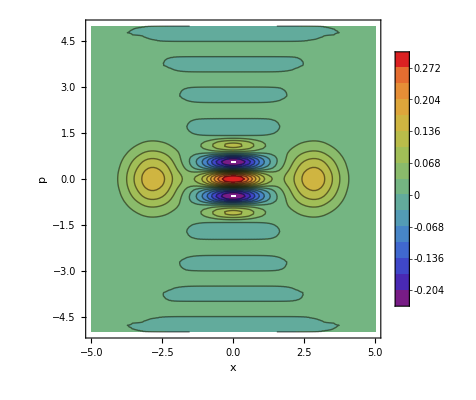

```mathematica
ListContourPlot[matCatExact2,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->Automatic,ColorFunction->"Rainbow",PlotRange->Full,AxesLabel->{x,p},LabelStyle->Large,Contours->15,InterpolationOrder->2,PlotLegends->Automatic]
```

```mathematica
ListPlot3D[matCatExact2,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->None,ColorFunction->"Rainbow",PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p},LabelStyle->Large,InterpolationOrder->2]
```

-Graphics3D-

```mathematica
N[Total[Total[matCatExact2]]](limits/range)^2
```

0.99977

### Calculation of the Wigner function using number states (and approx. by taking few terms) after noiseless attenuation

```mathematica
B[r_,t_]={{t,-r},{r,t}}; 
{ca0,cb0}=B[𝓇,𝓉].{ca,cb};
ψn[n_,x_]=(ⅇ^(-x^2/2)/(π^(1/4)√(n!2^n)))HermiteH[n,x];
ψin[α_,n_]=Expand[1/(√(2((1+ⅇ^(-2 Abs[α]^2)))))(ⅇ^((-Abs[α]^2)/2)∑_(n=0)^nlim ((α^n +(-α)^n)ca0^n )/n!)];
b=0;(* Post selection *)
α=2;
nlim=20;
coefftable=CoefficientList[ψin[α,nlim],{cb,ca}];
Pr=Chop[Table[Abs[√((i-1)!   (j-1)!)coefftable[[i,j]]]^2,{i,1,Dimensions[coefftable][[1]]},{j,1,Dimensions[coefftable][[2]]}]];
Dimensions[coefftable]
```

{21,21}

### w/ post selection

```mathematica
ψoutwps[x_]=FullSimplify[Total[Table[√(b!(i-1)!)coefftable[[b+1,i]]ψn[i-1,x],{i,1,Dimensions[coefftable][[2]]}]]];
```

#### results

```mathematica
𝓇=0.5;
𝓉=√(1-𝓇^2);
Wwps[x_,p_]:=(1/(Total[Pr,{2}][[b+1]]2π))NIntegrate[ⅇ^(-ⅈ p y)Conjugate[(ψoutwps[x-(1/2)y])] ψoutwps[x+(1/2)y],{y,-10,10}];
limits=5;
range=10;
wpsmat=Table[Re[Chop[Wwps[(x-1)(limits/range)-limits,(p-1)(limits/range)-limits]]],{p,1,2 range +1},{x,1,2 range +1}];
```

```mathematica
Total[wpsmat,2](limits/range)^2
```

0.999982

```mathematica
wpsmat={{0,0,0,-1.0901222355702025*^-10,-1.6649093206817454*^-9,-2.9914243620370815*^-8,-2.960656479267415*^-7,-1.723345225766866*^-6,-6.042667819149665*^-6,-0.00001279827010519001,-0.000016429004185584084,-0.000012798270105208731,-6.0426678191552815*^-6,-1.7233452257728571*^-6,-2.9606564792522035*^-7,-2.991424362297436*^-8,-1.6649093259239432*^-9,-1.0901222105293473*^-10,0,0,0},{0,0,-1.1204771094520577*^-10,-5.210390003203456*^-10,4.361290192732992*^-9,2.009417144666691*^-8,2.103105607099747*^-7,1.285501404634893*^-6,4.466390545313954*^-6,9.495750143203593*^-6,0.00001220066915404252,9.495750143198023*^-6,4.466390545315556*^-6,1.2855014046326462*^-6,2.103105607125958*^-7,2.0094171448410407*^-8,4.361290193481877*^-9,-5.210390003203456*^-10,-1.1204771071117909*^-10,0,0},{0,7.171455632716542*^-10,0,6.871101870512567*^-10,4.0579744456462854*^-8,3.753376315094788*^-8,5.311665485754967*^-7,2.981556454921079*^-6,0.000010331854513954787,0.000022059246592657833,0.000028133564810276406,0.00002205924659265954,0.00001033185451395701,2.9815564549208084*^-6,5.311665485747478*^-7,3.753376315085427*^-8,4.0579744452343984*^-8,6.87110187800142*^-10,0,7.171455632248489*^-10,0},{1.3295409717894056*^-9,1.5556283303319777*^-8,6.070718514455616*^-8,2.202397710946119*^-7,6.593621283436352*^-7,6.429013704810988*^-7,8.621922935121772*^-7,8.867676886434506*^-7,2.5170725886923093*^-6,4.928060050689964*^-6,6.4902600622759*^-6,4.928060050691275*^-6,2.517072588694813*^-6,8.867676886447378*^-7,8.621922935072159*^-7,6.429013704811924*^-7,6.59362128344434*^-7,2.2023977109456507*^-7,6.070718514455616*^-8,1.5556283303378834*^-8,1.3295409717912306*^-9},{2.859758622362819*^-8,3.136770813379824*^-7,1.7723375014031336*^-6,6.375281537505556*^-6,0.00001465581773878302,0.000019272122916805784,0.000015282196262075734,2.562960374526547*^-6,-0.00001544673560490952,-0.00003818618613364086,-0.00004903181736799969,-0.000038186186133638616,-0.000015446735604910268,2.5629603745237386*^-6,0.00001528219626207386,0.00001927212291680541,0.000014655817738786952,6.3752815375049*^-6,1.7723375014028293*^-6,3.1367708133810235*^-7,2.8597586223626362*^-8},{4.455662040963568*^-7,4.6102663844973*^-6,0.00002780646661465041,0.00010145209808343568,0.00022655287761040417,0.0003066620279505417,0.0002606246028629887,0.00018264802389035892,0.00024009177233953906,0.000436460692131254,0.0005526627492285596,0.00043646069213125385,0.00024009177233954017,0.0001826480238903577,0.00026062460286299427,0.0003066620279505422,0.00022655287761040376,0.00010145209808343568,0.000027806466614650294,4.610266384497291*^-6,4.4556620409636263*^-7},{4.306272157013753*^-6,0.00004333280434296136,0.0002629137911446395,0.0009644380925947803,0.002146884762959621,0.0028900197592199857,0.002276830826333183,0.0006102666297449841,-0.0016333682200687571,-0.004145666723614276,-0.005392751900483285,-0.004145666723614275,-0.001633368220068758,0.0006102666297449869,0.002276830826333183,0.0028900197592199913,0.002146884762959618,0.0009644380925947811,0.0002629137911446395,0.00004333280434296136,4.306272157013741*^-6},{0.000025023497719253924,0.0002495883680378762,0.001511720242796187,0.0055503648687223175,0.01236044152896677,0.01672196456764952,0.013969601412294613,0.008505616446936126,0.00802492771357132,0.01303188763697124,0.01633226000146364,0.01303188763697123,0.008024927713571313,0.008505616446936122,0.013969601412294613,0.016721964567649517,0.012360441528966771,0.005550364868722318,0.0015117202427961868,0.0002495883680378762,0.00002502349771925393},{0.00008749013399499653,0.0008719319818907225,0.005276718840757357,0.019372094349545527,0.04313794376110061,0.05829818848269035,0.04811814900142736,0.025996450405753838,0.015127372436457806,0.018214028886743536,0.021987510033058568,0.018214028886743512,0.015127372436457802,0.025996450405753838,0.04811814900142734,0.05829818848269035,0.04313794376110062,0.01937209434954553,0.0052767188407573575,0.0008719319818907228,0.00008749013399499653},{0.00018496800227946696,0.0018457439310206282,0.01117110041164221,0.0410097251332996,0.09129390795376659,0.12296097692589313,0.09753690594877883,0.030123807533324876,-0.05492130163954078,-0.1455056604847015,-0.18979627264361784,-0.1455056604847015,-0.05492130163954078,0.03012380753332488,0.0975369059487788,0.12296097692589307,0.09129390795376661,0.041009725133299604,0.01117110041164221,0.0018457439310206282,0.00018496800227946696},{0.00023730177277487391,0.00236956625108632,0.014343746091715076,0.05266015240240708,0.11729294087433363,0.15896957344497245,0.13553234444261317,0.09791028664974928,0.1362146525041552,0.2508249876203356,0.31826069897188874,0.2508249876203356,0.13621465250415524,0.09791028664974927,0.13553234444261317,0.15896957344497242,0.11729294087433359,0.05266015240240708,0.014343746091715076,0.00236956625108632,0.00023730177277487391},{0.00018496800227946696,0.0018457439310206282,0.01117110041164221,0.0410097251332996,0.09129390795376659,0.12296097692589313,0.09753690594877883,0.030123807533324876,-0.05492130163954078,-0.1455056604847015,-0.18979627264361784,-0.1455056604847015,-0.05492130163954078,0.03012380753332488,0.0975369059487788,0.12296097692589307,0.09129390795376661,0.041009725133299604,0.01117110041164221,0.0018457439310206282,0.00018496800227946696},{0.00008749013399499653,0.0008719319818907225,0.005276718840757357,0.019372094349545527,0.04313794376110061,0.05829818848269035,0.04811814900142736,0.025996450405753838,0.015127372436457806,0.018214028886743536,0.021987510033058568,0.018214028886743512,0.015127372436457802,0.025996450405753838,0.04811814900142734,0.05829818848269035,0.04313794376110062,0.01937209434954553,0.0052767188407573575,0.0008719319818907228,0.00008749013399499653},{0.000025023497719253924,0.0002495883680378762,0.001511720242796187,0.0055503648687223175,0.01236044152896677,0.01672196456764952,0.013969601412294613,0.008505616446936126,0.00802492771357132,0.01303188763697124,0.01633226000146364,0.01303188763697123,0.008024927713571313,0.008505616446936122,0.013969601412294613,0.016721964567649517,0.012360441528966771,0.005550364868722318,0.0015117202427961868,0.0002495883680378762,0.00002502349771925393},{4.306272157013753*^-6,0.00004333280434296136,0.0002629137911446395,0.0009644380925947803,0.002146884762959621,0.0028900197592199857,0.002276830826333183,0.0006102666297449841,-0.0016333682200687571,-0.004145666723614276,-0.005392751900483285,-0.004145666723614275,-0.001633368220068758,0.0006102666297449869,0.002276830826333183,0.0028900197592199913,0.002146884762959618,0.0009644380925947811,0.0002629137911446395,0.00004333280434296136,4.306272157013741*^-6},{4.455662040963568*^-7,4.6102663844973*^-6,0.00002780646661465041,0.00010145209808343568,0.00022655287761040417,0.0003066620279505417,0.0002606246028629887,0.00018264802389035892,0.00024009177233953906,0.000436460692131254,0.0005526627492285596,0.00043646069213125385,0.00024009177233954017,0.0001826480238903577,0.00026062460286299427,0.0003066620279505422,0.00022655287761040376,0.00010145209808343568,0.000027806466614650294,4.610266384497291*^-6,4.4556620409636263*^-7},{2.859758622362819*^-8,3.136770813379824*^-7,1.7723375014031336*^-6,6.375281537505556*^-6,0.00001465581773878302,0.000019272122916805784,0.000015282196262075734,2.562960374526547*^-6,-0.00001544673560490952,-0.00003818618613364086,-0.00004903181736799969,-0.000038186186133638616,-0.000015446735604910268,2.5629603745237386*^-6,0.00001528219626207386,0.00001927212291680541,0.000014655817738786952,6.3752815375049*^-6,1.7723375014028293*^-6,3.1367708133810235*^-7,2.8597586223626362*^-8},{1.3295409717894056*^-9,1.5556283303319777*^-8,6.070718514455616*^-8,2.202397710946119*^-7,6.593621283436352*^-7,6.429013704810988*^-7,8.621922935121772*^-7,8.867676886434506*^-7,2.5170725886923093*^-6,4.928060050689964*^-6,6.4902600622759*^-6,4.928060050691275*^-6,2.517072588694813*^-6,8.867676886447378*^-7,8.621922935072159*^-7,6.429013704811924*^-7,6.59362128344434*^-7,2.2023977109456507*^-7,6.070718514455616*^-8,1.5556283303378834*^-8,1.3295409717912306*^-9},{0,7.171455632716542*^-10,0,6.871101870512567*^-10,4.0579744456462854*^-8,3.753376315094788*^-8,5.311665485754967*^-7,2.981556454921079*^-6,0.000010331854513954787,0.000022059246592657833,0.000028133564810276406,0.00002205924659265954,0.00001033185451395701,2.9815564549208084*^-6,5.311665485747478*^-7,3.753376315085427*^-8,4.0579744452343984*^-8,6.87110187800142*^-10,0,7.171455632248489*^-10,0},{0,0,-1.1204771094520577*^-10,-5.210390003203456*^-10,4.361290192732992*^-9,2.009417144666691*^-8,2.103105607099747*^-7,1.285501404634893*^-6,4.466390545313954*^-6,9.495750143203593*^-6,0.00001220066915404252,9.495750143198023*^-6,4.466390545315556*^-6,1.2855014046326462*^-6,2.103105607125958*^-7,2.0094171448410407*^-8,4.361290193481877*^-9,-5.210390003203456*^-10,-1.1204771071117909*^-10,0,0},{0,0,0,-1.0901222355702025*^-10,-1.6649093206817454*^-9,-2.9914243620370815*^-8,-2.960656479267415*^-7,-1.723345225766866*^-6,-6.042667819149665*^-6,-0.00001279827010519001,-0.000016429004185584084,-0.000012798270105208731,-6.0426678191552815*^-6,-1.7233452257728571*^-6,-2.9606564792522035*^-7,-2.991424362297436*^-8,-1.6649093259239432*^-9,-1.0901222105293473*^-10,0,0,0}};
```

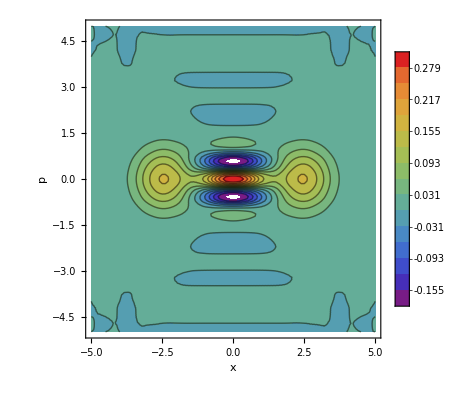

```mathematica
ListContourPlot[wpsmat,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->Automatic,ColorFunction->"Rainbow",PlotRange->Full,AxesLabel->{x,p},LabelStyle->Large,Contours->15,InterpolationOrder->2,PlotLegends->Automatic]
```

```mathematica
ListPlot3D[wpsmat,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->None,ColorFunction->"Rainbow",PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p},LabelStyle->Large,InterpolationOrder->2]
ClearAll[𝓇,𝓉]
```

### w/o post selection

```mathematica
Dimensions[coefftable][[1]]
```

21

```mathematica
ψn[21,x]
```

(ⅇ^(-x^2/2) (28158588057600 x-187723920384000 x^3+337903056691200 x^5-257449947955200 x^7+100119424204800 x^9-21844238008320 x^11+2800543334400 x^13-213374730240 x^15+9413591040 x^17-220200960 x^19+2097152 x^21))/(7431782400 √1939938 π^(1/4))

```mathematica
ψoutwops[x_]=Total[Table[√((i-1)!(j-1)!)coefftable[[i,j]]ψn[j-1,x],{i,1,Dimensions[coefftable][[1]]},{j,1,Dimensions[coefftable][[2]]}],{2}];
Dimensions[ψoutwops[x]]
```

{21}

```mathematica
𝓇=0.5;
𝓉=√(1-𝓇^2);
(*Wwops[x_,p_]:=Total[Table[(Total[Pr,{2}][[i]]/(2π))NIntegrate[ⅇ^(-ⅈ p y)(ψoutwops[x-(1/2)y][[i]])^*ψoutwops[x+(1/2)y][[i]],{y,-10,10}],{i,Dimensions[coefftable][[1]]}]];*)
Wwops[x_,p_]:=Total[Table[1/(2π)NIntegrate[ⅇ^(-ⅈ p y)Conjugate[(ψoutwops[x-(1/2)y][[i]])] ψoutwops[x+(1/2)y][[i]],{y,-10,10}],{i,Dimensions[coefftable][[1]]}]];
```

```mathematica
limits=5;
range=10;
wopsmat=Table[Re[Chop[Wwops[(x-1)(limits/range)-limits,(p-1)(limits/range)-limits]]],{p,1,2 range +1},{x,1,2 range +1}];
Total[wopsmat,2](limits/range)^2
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {-1.05484}. NIntegrate obtained 3.44997×10^-38+2.8026×10^-45 ⅈ and 5.21746×10^-43 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {-1.05484}. NIntegrate obtained 5.40191×10^-42+9.57919×10^-48 ⅈ and 1.63191×10^-46 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {-0.195468}. NIntegrate obtained 3.63173×10^-36-5.02225×10^-42 ⅈ and 3.86301×10^-41 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

0.999975

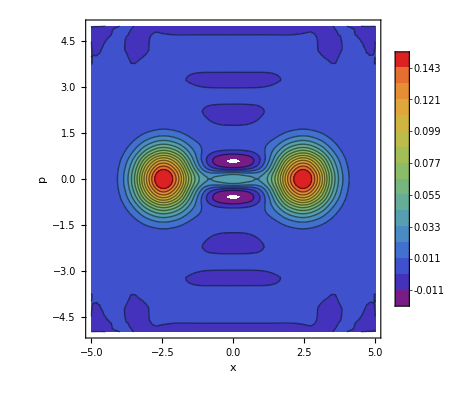

```mathematica
ListContourPlot[wopsmat,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->Automatic,ColorFunction->"Rainbow",PlotRange->Full,AxesLabel->{x,p},LabelStyle->Large,Contours->15,InterpolationOrder->2,PlotLegends->Automatic,AxesLabel->{x,p}]
```

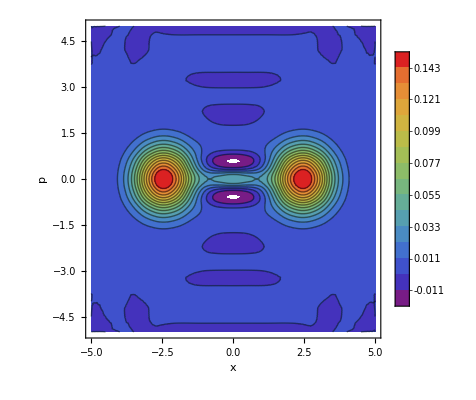

```mathematica
ListContourPlot[wopsmat,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->Automatic,ColorFunction->"Rainbow",PlotRange->Full,AxesLabel->{x,p},LabelStyle->Large,Contours->15,InterpolationOrder->2,PlotLegends->Automatic,AxesLabel->{x,p}]
```

```mathematica
wopsmat={{0,0,0,0,-3.2530141232395967*^-10,-3.922284103632225*^-9,-4.056577912504829*^-8,-2.3515758890783015*^-7,-8.195153088184555*^-7,-1.7354301007917874*^-6,-2.2284800743672005*^-6,-1.7354301007912483*^-6,-8.195153088184347*^-7,-2.3515758890603814*^-7,-4.056577912526037*^-8,-3.9222841034687404*^-9,-3.253014131105081*^-10,0,0,0,0},{0,0,1.7852794046734056*^-10,-5.997506467385404*^-10,-4.2080493276863475*^-10,7.689844044635357*^-9,2.6253482218991734*^-8,1.7308947714598362*^-7,6.121211472726207*^-7,1.2847697204716354*^-6,1.655653055125945*^-6,1.2847697204719469*^-6,6.121211472732821*^-7,1.7308947714640748*^-7,2.625348221997076*^-8,7.689844044904225*^-9,-4.208049335689205*^-10,-5.997506470919932*^-10,1.7852794045133515*^-10,0,0},{0,7.220897107126093*^-10,3.742706809558968*^-9,-2.4020171881307038*^-9,9.342711760672075*^-9,5.628850972560719*^-8,4.665028487636208*^-8,4.326739333930436*^-7,1.4063669625591006*^-6,2.9731081167747507*^-6,3.840932201443015*^-6,2.9731081167764215*^-6,1.4063669625581253*^-6,4.326739333926909*^-7,4.665028487851629*^-8,5.628850972388625*^-8,9.342711760650534*^-9,-2.4020171889285997*^-9,3.742706809399321*^-9,7.220897107041996*^-10,0},{5.501096343661597*^-10,1.4587611633734095*^-8,8.973717083136042*^-8,2.0673775049100584*^-7,5.334164472632214*^-7,8.744049820507226*^-7,5.178008509253062*^-7,4.906229460669702*^-7,3.485719577499334*^-7,7.44181939899886*^-7,8.234009504023333*^-7,7.441819399010595*^-7,3.4857195774994043*^-7,4.906229460677671*^-7,5.178008509249936*^-7,8.74404982047738*^-7,5.334164472628686*^-7,2.0673775049060326*^-7,8.973717083126605*^-8,1.4587611633715887*^-8,5.501096343630631*^-10},{2.325810751782446*^-8,2.960577549787813*^-7,1.8918019216930846*^-6,6.437769796075519*^-6,0.000014332314347402433,0.000019800135125763972,0.000015759530220813052,7.362880313101711*^-6,-1.0397915862306374*^-7,-4.754545562490939*^-6,-6.588574085818644*^-6,-4.7545455624920735*^-6,-1.039791586231831*^-7,7.362880313102955*^-6,0.000015759530220812042,0.00001980013512576138,0.000014332314347401514,6.437769796075783*^-6,1.8918019216931683*^-6,2.960577549787673*^-7,2.325810751782438*^-8},{4.291703776658644*^-7,4.499206503888497*^-6,0.000028009145633864044,0.00010209207013580962,0.0002264582273146525,0.0003067090015334356,0.0002522368255858276,0.00013258569751006368,0.00006508738478719861,0.00006513644964717292,0.00007631238907899114,0.00006513644964717149,0.0000650873847871994,0.00013258569751006357,0.00025223682558582234,0.0003067090015334346,0.00022645822731465337,0.0001020920701358094,0.00002800914563386405,4.499206503888527*^-6,4.291703776658642*^-7},{4.3181038934590705*^-6,0.00004313070635007128,0.00026310270138388926,0.0009671619069213643,0.0021519359510772974,0.0029052248820296066,0.002367504563635544,0.0011056613878408182,0.00008671642296053151,-0.0005054939263239717,-0.0007189095208396129,-0.0005054939263239701,0.00008671642296053086,0.0011056613878408167,0.0023675045636355413,0.002905224882029606,0.002151935951077299,0.000967161906921364,0.00026310270138388926,0.000043130706350071304,4.318103893459071*^-6},{0.000025231716759162608,0.0002501409046831163,0.0015141620617536284,0.005561958060996409,0.012385366458524238,0.01673068391242834,0.013741818535207428,0.007039698137802609,0.0028622498397826704,0.002094076791231212,0.0022869485093492507,0.0020940767912312136,0.0028622498397826695,0.007039698137802608,0.013741818535207428,0.016730683912428344,0.012385366458524238,0.005561958060996408,0.0015141620617536284,0.0002501409046831163,0.000025231716759162605},{0.00008794702647309572,0.0008746026783093242,0.005288495733818975,0.019413271360837564,0.04322800681768751,0.058386748198968955,0.04787666820135681,0.024070378854809883,0.008243078558068686,0.0036103018311486016,0.0032329554846668132,0.0036103018311485955,0.008243078558068688,0.02407037885480988,0.04787666820135681,0.058386748198968955,0.0432280068176875,0.019413271360837564,0.005288495733818974,0.0008746026783093243,0.00008794702647309572},{0.0001852684938998556,0.0018498181178204065,0.01119554742925141,0.04109865361755457,0.09150985926508787,0.12354285288420735,0.10076780456985238,0.047578509401796885,0.0056585203216591,-0.01732081991645441,-0.02521002316725275,-0.017320819916454403,0.0056585203216591,0.047578509401796885,0.10076780456985238,0.12354285288420735,0.09150985926508787,0.04109865361755457,0.01119554742925141,0.0018498181178204065,0.0001852684938998556},{0.00023735202941654784,0.0023736488359234888,0.014373585970823447,0.0527714129381836,0.11751033386803487,0.1587792896589003,0.1307843747547207,0.06912517644759722,0.03530416692623072,0.0371170958717925,0.043846188442328266,0.03711709587179253,0.035304166926230736,0.06912517644759722,0.13078437475472068,0.15877928965890029,0.11751033386803487,0.052771412938183604,0.014373585970823449,0.0023736488359234883,0.00023735202941654784},{0.0001852684938998556,0.0018498181178204065,0.01119554742925141,0.04109865361755457,0.09150985926508787,0.12354285288420735,0.10076780456985238,0.047578509401796885,0.0056585203216591,-0.01732081991645441,-0.02521002316725275,-0.017320819916454403,0.0056585203216591,0.047578509401796885,0.10076780456985238,0.12354285288420735,0.09150985926508787,0.04109865361755457,0.01119554742925141,0.0018498181178204065,0.0001852684938998556},{0.00008794702647309572,0.0008746026783093242,0.005288495733818975,0.019413271360837564,0.04322800681768751,0.058386748198968955,0.04787666820135681,0.024070378854809883,0.008243078558068686,0.0036103018311486016,0.0032329554846668132,0.0036103018311485955,0.008243078558068688,0.02407037885480988,0.04787666820135681,0.058386748198968955,0.0432280068176875,0.019413271360837564,0.005288495733818974,0.0008746026783093243,0.00008794702647309572},{0.000025231716759162608,0.0002501409046831163,0.0015141620617536284,0.005561958060996409,0.012385366458524238,0.01673068391242834,0.013741818535207428,0.007039698137802609,0.0028622498397826704,0.002094076791231212,0.0022869485093492507,0.0020940767912312136,0.0028622498397826695,0.007039698137802608,0.013741818535207428,0.016730683912428344,0.012385366458524238,0.005561958060996408,0.0015141620617536284,0.0002501409046831163,0.000025231716759162605},{4.3181038934590705*^-6,0.00004313070635007128,0.00026310270138388926,0.0009671619069213643,0.0021519359510772974,0.0029052248820296066,0.002367504563635544,0.0011056613878408182,0.00008671642296053151,-0.0005054939263239717,-0.0007189095208396129,-0.0005054939263239701,0.00008671642296053086,0.0011056613878408167,0.0023675045636355413,0.002905224882029606,0.002151935951077299,0.000967161906921364,0.00026310270138388926,0.000043130706350071304,4.318103893459071*^-6},{4.291703776658644*^-7,4.499206503888497*^-6,0.000028009145633864044,0.00010209207013580962,0.0002264582273146525,0.0003067090015334356,0.0002522368255858276,0.00013258569751006368,0.00006508738478719861,0.00006513644964717292,0.00007631238907899114,0.00006513644964717149,0.0000650873847871994,0.00013258569751006357,0.00025223682558582234,0.0003067090015334346,0.00022645822731465337,0.0001020920701358094,0.00002800914563386405,4.499206503888527*^-6,4.291703776658642*^-7},{2.325810751782446*^-8,2.960577549787813*^-7,1.8918019216930846*^-6,6.437769796075519*^-6,0.000014332314347402433,0.000019800135125763972,0.000015759530220813052,7.362880313101711*^-6,-1.0397915862306374*^-7,-4.754545562490939*^-6,-6.588574085818644*^-6,-4.7545455624920735*^-6,-1.039791586231831*^-7,7.362880313102955*^-6,0.000015759530220812042,0.00001980013512576138,0.000014332314347401514,6.437769796075783*^-6,1.8918019216931683*^-6,2.960577549787673*^-7,2.325810751782438*^-8},{5.501096343661597*^-10,1.4587611633734095*^-8,8.973717083136042*^-8,2.0673775049100584*^-7,5.334164472632214*^-7,8.744049820507226*^-7,5.178008509253062*^-7,4.906229460669702*^-7,3.485719577499334*^-7,7.44181939899886*^-7,8.234009504023333*^-7,7.441819399010595*^-7,3.4857195774994043*^-7,4.906229460677671*^-7,5.178008509249936*^-7,8.74404982047738*^-7,5.334164472628686*^-7,2.0673775049060326*^-7,8.973717083126605*^-8,1.4587611633715887*^-8,5.501096343630631*^-10},{0,7.220897107126093*^-10,3.742706809558968*^-9,-2.4020171881307038*^-9,9.342711760672075*^-9,5.628850972560719*^-8,4.665028487636208*^-8,4.326739333930436*^-7,1.4063669625591006*^-6,2.9731081167747507*^-6,3.840932201443015*^-6,2.9731081167764215*^-6,1.4063669625581253*^-6,4.326739333926909*^-7,4.665028487851629*^-8,5.628850972388625*^-8,9.342711760650534*^-9,-2.4020171889285997*^-9,3.742706809399321*^-9,7.220897107041996*^-10,0},{0,0,1.7852794046734056*^-10,-5.997506467385404*^-10,-4.2080493276863475*^-10,7.689844044635357*^-9,2.6253482218991734*^-8,1.7308947714598362*^-7,6.121211472726207*^-7,1.2847697204716354*^-6,1.655653055125945*^-6,1.2847697204719469*^-6,6.121211472732821*^-7,1.7308947714640748*^-7,2.625348221997076*^-8,7.689844044904225*^-9,-4.208049335689205*^-10,-5.997506470919932*^-10,1.7852794045133515*^-10,0,0},{0,0,0,0,-3.2530141232395967*^-10,-3.922284103632225*^-9,-4.056577912504829*^-8,-2.3515758890783015*^-7,-8.195153088184555*^-7,-1.7354301008013123*^-6,-2.2284800743672005*^-6,-1.7354301007912483*^-6,-8.195153088184347*^-7,-2.3515758890603814*^-7,-4.056577912526037*^-8,-3.9222841034687404*^-9,-3.253014131105081*^-10,0,0,0,0}};
```

```mathematica
ListPlot3D[wopsmat,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->None,ColorFunction->"Rainbow",PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p},LabelStyle->Large,InterpolationOrder->2]
```

-Graphics3D-

## Model fitting

### Before

```mathematica
ClearAll[A,α]
model=1((ⅇ^(-(x-√2 α)^2-p^2)+ⅇ^(-(x+√2 α)^2-p^2)+2 ⅇ^(-x^2-p^2)Cos[2 √2 α p])/(2π(1+ⅇ^(-2 Abs[α]^2))));
range =(Dimensions[wpsmat][[1]]-1)/2;
IdxData= Table[{(i-range -1)limits/range,(j-range-1)limits/range,wpsmat[[i,j]]},{i,1,2range+1},{j,1,2range+1}];
Data=Flatten[IdxData,1];
fit = FindFit[Data,model,{{A,1},{α,2}},{p,x}]
```

{A→1.,α→1.73208}

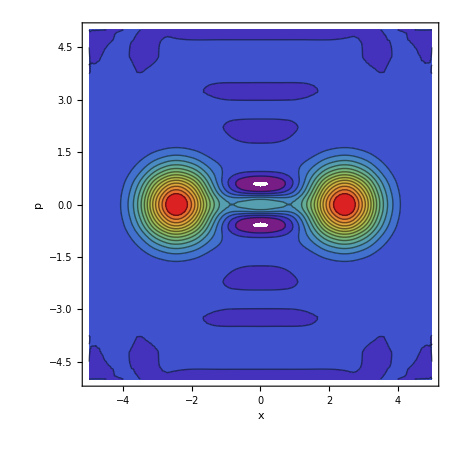

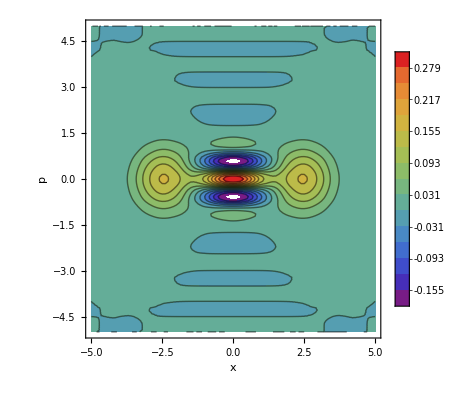

```mathematica
limits=5;
range=10;
α=1.7320841564785787;
matCatExact=Table[Re[Chop[WCatExact[α,nlim,(x-1)(limits/range)-limits,(p-1)(limits/range)-limits]]],{p,1,2 range +1},{x,1,2 range +1}];
ListContourPlot[matCatExact,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->Automatic,ColorFunction->"Rainbow",PlotRange->Full,AxesLabel->{x,p},LabelStyle->Large,Contours->15,InterpolationOrder->2,PlotLegends->Automatic,AxesLabel->{x,p}]
```

### After (w/ post selection)

```mathematica
ClearAll[A,α]
limits=3;
range=8;
model=((ⅇ^(-(x-√2 α)^2-p^2)+ⅇ^(-(x+√2 α)^2-p^2)+2 ⅇ^(-x^2-p^2)Cos[2 √2 α p])/(2π(1+ⅇ^(-2 Abs[α]^2))));
range =(Dimensions[wpsmat][[1]]-1)/2;
IdxData= Table[{(i-range -1)limits/range,(j-range-1)limits/range,wpsmat[[i,j]]},{i,1,2range+1},{j,1,2range+1}];
Data=Flatten[IdxData,1];
fit = FindFit[Data,model,{{A,1},{α,2}},{p,x}]
```

{A→1.,α→1.73198}

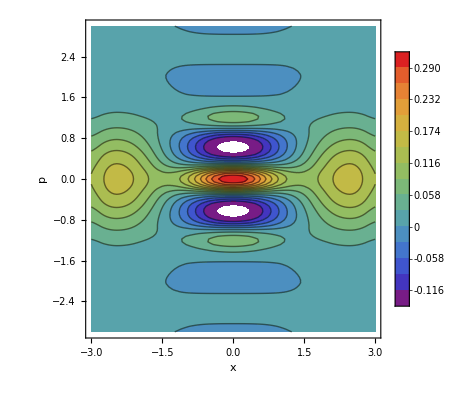

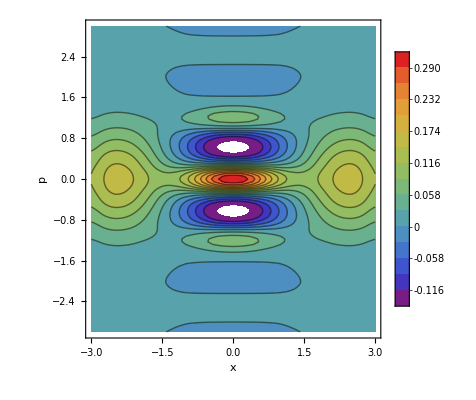

```mathematica
ψn[n_,x_]=(ⅇ^(-x^2/2)/(π^(1/4)√(n!2^n)))HermiteH[n,x];
ψc[α_,nlim_,x_]=ⅇ^((-Abs[α]^2)/2)∑_(n=0)^nlim (α^n (ⅇ^(-x^2/2)/(π^(1/4)√(n!2^n)))HermiteH[n,x] )/(√n!);
ψcExact[α_,nlim_,x_]=(1/π^(1/4))ⅇ^((-(x-√2 α)^2)/2);(*checked*)
ψCat[α_,nlim_,x_]=(ψc[α,nlim,x]+ψc[-α,nlim,x])/(√(2(1+ⅇ^(-2 Abs[α]^2))));
nlim=20;
WCat[α_,nlim_,x_,p_]:=(1/(2π))NIntegrate[ⅇ^(-ⅈ p y)Conjugate[(ψCat[α,nlim,x-y/2])] ψCat[α,nlim,x+y/2],{y,-10,10}];
WCatExact[α_,nlim_,x_,p_]:=(ⅇ^(-(x-√2 α)^2-p^2)+ⅇ^(-(x+√2 α)^2-p^2)+2 ⅇ^(-x^2-p^2)Cos[2 √2 α p])/(2π(1+ⅇ^(-2 Abs[α]^2)));(* Typo in https://arxiv.org/pdf/2006.16985.pdf Eq. (27) *)

limits=3;
range=8;
α=α/.fit;
matCatExact2=Table[Re[Chop[WCatExact[α,nlim,(x-1)(limits/range)-limits,(p-1)(limits/range)-limits]]],{p,1,2 range +1},{x,1,2 range +1}];ListContourPlot[matCatExact2,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->Automatic,ColorFunction->"Rainbow",PlotRange->Full,AxesLabel->{x,p},LabelStyle->Large,Contours->15,InterpolationOrder->2,PlotLegends->Automatic]
ListContourPlot[wpsmat2038,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->Automatic,ColorFunction->"Rainbow",PlotRange->Full,AxesLabel->{x,p},LabelStyle->Large,Contours->15,InterpolationOrder->2,PlotLegends->Automatic]
```

This tells the cat state is noiseless after post selection

## Effect of inefficient detector in noiseless attenuation

```mathematica
B[r_,t_]={{t,-r},{r,t}}; 
{ca0,cb0}=B[𝓇,𝓉].{ca,cb1};
{cb1,cdump0}=B[𝓇loss,𝓉loss].{cb,cdump};
ψn[n_,x_]=(ⅇ^(-x^2/2)/(π^(1/4)√(n!2^n)))HermiteH[n,x];
ψin[α_,n_]=Expand[1/(√(2((1+ⅇ^(-2 Abs[α]^2)))))(ⅇ^((-Abs[α]^2)/2)∑_(n=0)^nlim ((α^n +(-α)^n)ca0^n )/n!)];
b=0;(* Post selection *)
α=2;
nlim=20;
coefftable=CoefficientList[ψin[α,nlim],{cb,cdump,ca}];
Pr=Chop[Table[Abs[√((i-1)!   (j-1)!(k-1)!)coefftable[[i,j,k]]]^2,{i,1,Dimensions[coefftable][[1]]},{j,1,Dimensions[coefftable][[2]]},{k,1,Dimensions[coefftable][[3]]}]];
Dimensions[coefftable]
```

{21,21,21}

```mathematica
Chop[Total[Pr,{3}][[b+1]]]
```

{0.368668,0.0366844,0.00184334,0.0000611407,1.53612×10^-6,3.05704×10^-8,5.12038×10^-10,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
N[Pr[[1,20,1]]]
```

0.

#### w/ post selection

```mathematica
ψoutwps[x_]=FullSimplify[Total[Table[√(b!(i-1)!(j-1)!)coefftable[[b+1,i,j]]ψn[j-1,x],{i,1,Dimensions[coefftable][[2]]},{j,1,Dimensions[coefftable][[3]]}],{2}]];
```

#### results

```mathematica
𝓇=0.5;
𝓉=√(1-𝓇^2);
𝓇loss=√0.10;
𝓉loss=√(1-𝓇loss^2);
Wwpsp[x_,p_]:=(1/(Total[Pr,{2,3}][[b+1]]))(1/(2π))Total[Table[NIntegrate[ⅇ^(-ⅈ p y)Conjugate[(ψoutwps[x-(1/2)y][[i]])] ψoutwps[x+(1/2)y][[i]],{y,-10,10}],{i,1,Dimensions[coefftable][[2]]}]];
(*Wwpsp[x_,p_]:=∑_(i=1)^(Dimensions[coefftable][[2]]) (1/(Total[Pr,{3}][[b+1,i]]))(1/(2π))NIntegrate[ⅇ^(-ⅈ p y)(ψoutwps[x-(1/2)y][[i]])^*ψoutwps[x+(1/2)y][[i]],{y,-10,10}];*)

limits=5;
range=10;
wpsmatineff=Table[Re[Chop[Wwpsp[(x-1)(limits/range)-limits,(p-1)(limits/range)-limits]]],{p,1,2 range +1},{x,1,2 range +1}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0193758}. NIntegrate obtained 4.34684×10^-15+6.35275×10^-22 ⅈ and 1.48065×10^-20 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0193758}. NIntegrate obtained -3.0365×10^-16+6.03842×10^-23 ⅈ and 6.88919×10^-22 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0193758}. NIntegrate obtained 8.0516×10^-46+1.47472×10^-52 ⅈ and 1.13845×10^-51 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
wpsmatineff={{0,0,0,-1.0010112078654381*^-10,-1.3737896485104294*^-9,-2.450771998495514*^-8,-2.430438458404758*^-7,-1.412550812526325*^-6,-4.9498660007561295*^-6,-0.000010482962332402165,-0.000013456915540115845,-0.000010482962332418958,-4.949866000760275*^-6,-1.4125508125319347*^-6,-2.4304384583869243*^-7,-2.4507719986555192*^-8,-1.3737896536788144*^-9,-1.0010111829224605*^-10,0,0,0},{0,0,0,-6.257272264466823*^-10,3.8737122570249676*^-9,1.7444213912779816*^-8,1.7060867888035674*^-7,1.055776631546316*^-6,3.6598845116757114*^-6,7.776421095771776*^-6,9.99533719815536*^-6,7.776421095767667*^-6,3.659884511677151*^-6,1.0557766315443808*^-6,1.706086788827453*^-7,1.744421391427001*^-8,3.873712257511625*^-9,-6.257272264414263*^-10,0,0,0},{0,7.524512091762572*^-10,2.8184939482480083*^-10,-6.096588181073778*^-10,3.9305277304170033*^-8,3.607388495685012*^-8,4.2731648971255785*^-7,2.4616567810007377*^-6,8.452246542066674*^-6,0.000018071686746291375,0.000023045955005125518,0.00001807168674629356,8.45224654206853*^-6,2.461656781000389*^-6,4.2731648971117915*^-7,3.607388495667688*^-8,3.930527730053577*^-8,-6.09658817537875*^-10,2.818493953121213*^-10,7.524512091354764*^-10,0},{1.2637806760827085*^-9,1.5804930088992344*^-8,6.323904641099078*^-8,2.1305566246013423*^-7,6.595756947034982*^-7,6.599238901754644*^-7,8.068502855473077*^-7,8.025096037026028*^-7,2.0488873282450735*^-6,4.0836018944369916*^-6,5.26486680414252*^-6,4.083601894438876*^-6,2.048887328247188*^-6,8.025096037039595*^-7,8.068502855427958*^-7,6.599238901755551*^-7,6.59575694703976*^-7,2.1305566246030763*^-7,6.323904641096042*^-8,1.5804930089044358*^-8,1.2637806760847847*^-9},{2.8111260127931455*^-8,3.1401087370547064*^-7,1.7847917492760468*^-6,6.361196317852623*^-6,0.000014658954867588769,0.00001931950312484038,0.00001542435262483457,3.5330554681852164*^-6,-0.000012194706433536479,-0.000031253504821185993,-0.000040076125528268214,-0.000031253504821183974,-0.000012194706433537478,3.533055468182444*^-6,0.000015424352624832888,0.000019319503124840085,0.000014658954867592503,6.361196317852031*^-6,1.784791749275847*^-6,3.140108737055783*^-7,2.8111260127929245*^-8},{4.4376115473775077*^-7,4.6067876450407495*^-6,0.00002784501148954319,0.00010149498378690971,0.00022661639850208345,0.00030663300337668245,0.00025890040779820564,0.00017213088911728036,0.00020347472256720337,0.0003587679449096764,0.00045293994547428607,0.00035876794490967613,0.00020347472256720421,0.00017213088911727941,0.0002589004077982112,0.00030663300337668224,0.0002266163985020831,0.00010149498378690948,0.00002784501148954309,4.6067876450407385*^-6,4.437611547377568*^-7},{4.305739903808353*^-6,0.000043329467743273216,0.00026303689635802824,0.0009649138859029775,0.002147941434815309,0.0028932051946026,0.002295797990988821,0.0007139627121414439,-0.001273367034402973,-0.003383836958066527,-0.004414572291441964,-0.003383836958066526,-0.0012733670344029736,0.0007139627121414466,0.002295797990988821,0.002893205194602606,0.002147941434815306,0.0009649138859029779,0.00026303689635802824,0.000043329467743273196,4.305739903808341*^-6},{0.000025041762284017615,0.00024968454249363846,0.0015123516787684487,0.0055528529895994124,0.012365623070168457,0.016723798915898667,0.013921952717221972,0.008198823824395083,0.0069444355636713835,0.01074275438379545,0.013392761711876488,0.01074275438379544,0.006944435563671377,0.00819882382439508,0.013921952717221972,0.016723798915898664,0.01236562307016846,0.005552852989599413,0.0015123516787684485,0.00024968454249363846,0.00002504176228401762},{0.0000875479017313143,0.0008723609316126507,0.005279086077591283,0.019380748234970963,0.043156805507795826,0.058316722323032345,0.0480675920676709,0.025593329280076592,0.013686584761144895,0.015157664070346093,0.018062431240688317,0.01515766407034607,0.01368658476114489,0.025593329280076592,0.04806759206767088,0.058316722323032345,0.04315680550779583,0.019380748234970966,0.0052790860775912855,0.0008723609316126509,0.0000875479017313143},{0.00018504889261403804,0.001846586482074152,0.011176140075673531,0.0410282863095944,0.09133909539557736,0.1230827453282016,0.09821308106628529,0.0337768472385836,-0.04224275068102603,-0.11867828183682026,-0.15535056344686551,-0.11867828183682026,-0.04224275068102603,0.03377684723858361,0.09821308106628528,0.12308274532820157,0.09133909539557739,0.04102828630959442,0.011176140075673531,0.001846586482074152,0.00018504889261403804},{0.0002373823143571388,0.002370581571986924,0.01435013964487101,0.0526834857513911,0.11733844660738364,0.15892976586482654,0.13453868344178638,0.09188595930015932,0.11509543140302282,0.20609877231814425,0.26082939858228776,0.20609877231814425,0.11509543140302284,0.09188595930015932,0.13453868344178638,0.15892976586482654,0.1173384466073836,0.0526834857513911,0.01435013964487101,0.002370581571986924,0.0002373823143571388},{0.00018504889261403804,0.001846586482074152,0.011176140075673531,0.0410282863095944,0.09133909539557736,0.1230827453282016,0.09821308106628529,0.0337768472385836,-0.04224275068102603,-0.11867828183682026,-0.15535056344686551,-0.11867828183682026,-0.04224275068102603,0.03377684723858361,0.09821308106628528,0.12308274532820157,0.09133909539557739,0.04102828630959442,0.011176140075673531,0.001846586482074152,0.00018504889261403804},{0.0000875479017313143,0.0008723609316126507,0.005279086077591283,0.019380748234970963,0.043156805507795826,0.058316722323032345,0.0480675920676709,0.025593329280076592,0.013686584761144895,0.015157664070346093,0.018062431240688317,0.01515766407034607,0.01368658476114489,0.025593329280076592,0.04806759206767088,0.058316722323032345,0.04315680550779583,0.019380748234970966,0.0052790860775912855,0.0008723609316126509,0.0000875479017313143},{0.000025041762284017615,0.00024968454249363846,0.0015123516787684487,0.0055528529895994124,0.012365623070168457,0.016723798915898667,0.013921952717221972,0.008198823824395083,0.0069444355636713835,0.01074275438379545,0.013392761711876488,0.01074275438379544,0.006944435563671377,0.00819882382439508,0.013921952717221972,0.016723798915898664,0.01236562307016846,0.005552852989599413,0.0015123516787684485,0.00024968454249363846,0.00002504176228401762},{4.305739903808353*^-6,0.000043329467743273216,0.00026303689635802824,0.0009649138859029775,0.002147941434815309,0.0028932051946026,0.002295797990988821,0.0007139627121414439,-0.001273367034402973,-0.003383836958066527,-0.004414572291441964,-0.003383836958066526,-0.0012733670344029736,0.0007139627121414466,0.002295797990988821,0.002893205194602606,0.002147941434815306,0.0009649138859029779,0.00026303689635802824,0.000043329467743273196,4.305739903808341*^-6},{4.4376115473775077*^-7,4.6067876450407495*^-6,0.00002784501148954319,0.00010149498378690971,0.00022661639850208345,0.00030663300337668245,0.00025890040779820564,0.00017213088911728036,0.00020347472256720337,0.0003587679449096764,0.00045293994547428607,0.00035876794490967613,0.00020347472256720421,0.00017213088911727941,0.0002589004077982112,0.00030663300337668224,0.0002266163985020831,0.00010149498378690948,0.00002784501148954309,4.6067876450407385*^-6,4.437611547377568*^-7},{2.8111260127931455*^-8,3.1401087370547064*^-7,1.7847917492760468*^-6,6.361196317852623*^-6,0.000014658954867588769,0.00001931950312484038,0.00001542435262483457,3.5330554681852164*^-6,-0.000012194706433536479,-0.000031253504821185993,-0.000040076125528268214,-0.000031253504821183974,-0.000012194706433537478,3.533055468182444*^-6,0.000015424352624832888,0.000019319503124840085,0.000014658954867592503,6.361196317852031*^-6,1.784791749275847*^-6,3.140108737055783*^-7,2.8111260127929245*^-8},{1.2637806760827085*^-9,1.5804930088992344*^-8,6.323904641099078*^-8,2.1305566246013423*^-7,6.595756947034982*^-7,6.599238901754644*^-7,8.068502855473077*^-7,8.025096037026028*^-7,2.0488873282450735*^-6,4.0836018944369916*^-6,5.26486680414252*^-6,4.083601894438876*^-6,2.048887328247188*^-6,8.025096037039595*^-7,8.068502855427958*^-7,6.599238901755551*^-7,6.59575694703976*^-7,2.1305566246030763*^-7,6.323904641096042*^-8,1.5804930089044358*^-8,1.2637806760847847*^-9},{0,7.524512091762572*^-10,2.8184939482480083*^-10,-6.096588181073778*^-10,3.9305277304170033*^-8,3.607388495685012*^-8,4.2731648971255785*^-7,2.4616567810007377*^-6,8.452246542066674*^-6,0.000018071686746291375,0.000023045955005125518,0.00001807168674629356,8.45224654206853*^-6,2.461656781000389*^-6,4.2731648971117915*^-7,3.607388495667688*^-8,3.930527730053577*^-8,-6.09658817537875*^-10,2.818493953121213*^-10,7.524512091354764*^-10,0},{0,0,0,-6.257272264466823*^-10,3.8737122570249676*^-9,1.7444213912779816*^-8,1.7060867888035674*^-7,1.055776631546316*^-6,3.6598845116757114*^-6,7.776421095771776*^-6,9.99533719815536*^-6,7.776421095767667*^-6,3.659884511677151*^-6,1.0557766315443808*^-6,1.706086788827453*^-7,1.744421391427001*^-8,3.873712257511625*^-9,-6.257272264414263*^-10,0,0,0},{0,0,0,-1.0010112078654381*^-10,-1.3737896485104294*^-9,-2.450771998495514*^-8,-2.430438458404758*^-7,-1.412550812526325*^-6,-4.9498660007561295*^-6,-0.000010482962332402165,-0.000013456915540115845,-0.000010482962332418958,-4.949866000760275*^-6,-1.4125508125319347*^-6,-2.4304384583869243*^-7,-2.4507719986555192*^-8,-1.3737896536788144*^-9,-1.0010111829224605*^-10,0,0,0}};
```

```mathematica
Total[wpsmatineff,2](limits/range)^2
```

0.999981

```mathematica
ListContourPlot[wpsmatineff,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->Automatic,ColorFunction->"Rainbow",PlotRange->Full,AxesLabel->{x,p},LabelStyle->Large,Contours->15,InterpolationOrder->2,PlotLegends->Automatic]
```

-Graphics-

```mathematica
ListPlot3D[wpsmatineff,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->None,ColorFunction->"Rainbow",PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p},LabelStyle->Large,InterpolationOrder->2]
ClearAll[𝓇,𝓉]
```

-Graphics3D-

#### w/o post selection

```mathematica
ψoutwops[x_]=FullSimplify[Total[Table[√((i-1)!(j-1)!(k-1)!)coefftable[[i,j,k]]ψn[k-1,x],{i,1,Dimensions[coefftable][[1]]},{j,1,Dimensions[coefftable][[2]]},{k,1,Dimensions[coefftable][[3]]}],{3}]];
Dimensions[ψoutwops[x]]
```

{21,21}

#### results

```mathematica
Re[Chop[Wwops[0.5,0.5]]]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

-0.0536432

```mathematica
ClearAll[Wwops,𝓇,𝓉]
```

```mathematica
𝓇=0.5;
𝓉=√(1-𝓇^2);
𝓇loss=√0.10;
𝓉loss=√(1-𝓇^2);
Wwops[x_,p_]:=Total[Table[1/(2π)NIntegrate[Chop[ⅇ^(-ⅈ p y)Conjugate[(ψoutwops[x-(1/2)y][[i,j]])] ψoutwops[x+(1/2)y][[i,j]]],{y,-10,10}],{i,Dimensions[coefftable][[1]]},{j,Dimensions[coefftable][[2]]}],2];
```

```mathematica
limits=5;
range=10;
wopsmat=Table[Re[Chop[Wwops[(x-1)(limits/range)-limits,(p-1)(limits/range)-limits]]],{p,1,2 range +1},{x,1,2 range +1}];
ListContourPlot[wopsmat,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->Automatic,ColorFunction->"Rainbow",PlotRange->Full,AxesLabel->{x,p},LabelStyle->Large,Contours->15,InterpolationOrder->2,PlotLegends->Automatic,AxesLabel->{x,p}]

ListPlot3D[wopsmat,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->None,ColorFunction->"Rainbow",PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p},LabelStyle->Large,InterpolationOrder->2]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

$Aborted

-Graphics-

-Graphics3D-